# 7. CAMINOS Y CICLOS

*Las entradas de cada ejemplo deben ser ejecutados en orden para su correcto funcionamiento.

1. DEFINICIÓN Y TIPOS DE CAMINOS

### 1.1. CAMINOS EN GRAFOS NO DIRIGIDOS

#### Ejemplo 7.1.

```mathematica
caminovertices={1,2,3,4,5,1,5,4,2};
```

```mathematica
caminolados={1->2,2->3,3->4,4->5,5->1,1->5,5->4,4->2};
```

```mathematica
caminolados2={1->2,3->2,4->3,5->4,5->1,5->1,5->4,2->4};
```

```mathematica
caminolados={1,1->2,2,2->3,3,3->4,4,4->5,5,5->1,1,1->5,5,5->4,4,4->2,2};
```

#### Función 7.1. CAMINO[]

```mathematica
CAMINO[camino_,F_]:=Module[{i},
cam=True;
Do[If[Intersection[{camino[[i]]->camino[[i+1]],
camino[[i+1]]->camino[[i]]},F]=={},cam=False;Break[];]
,{i,Length[camino]-1}];
cam
]
```

#### Función 7.2. CAMINO2[]

```mathematica
CAMINO2[camino_,matrizadyacencia_]:=Module[{i},
cam=True;
Do[If[matrizadyacencia[[camino[[i]],camino[[i+1]]]]==0,cam=False;Break[];],{i,Length[camino]-1}];
cam
]
```

#### Función 7.3. SUCLADOS[]

```mathematica
SUCLADOS[vertices_]:=Module[{i},
lados={};
Do[AppendTo[lados,vertices[[i]]->vertices[[i+1]]];,{i,Length[vertices]-1}];
lados
]
```

#### Función 7.4. SUCVERTICES[]

```mathematica
SUCVERTICES[lados_]:=Module[{i},
vertices={lados[[1]][[1]]};
Do[AppendTo[vertices,lados[[i]][[2]]];,{i,Length[lados]}];
vertices
]
```

#### Ejemplo 7.2.

```mathematica
K5=Table[If[i==j,0,1],{i,5},{j,5}];
```

```mathematica
CAMINO2[camino_,matrizadyacencia_]:=Module[{i},
cam=True;
Do[If[matrizadyacencia[[camino[[i]],camino[[i+1]]]]==0,cam=False;Break[];],{i,Length[camino]-1}];
cam
]
```

```mathematica
CAMINO2[{1,2,3,4,5,1},K5]
```

True

```mathematica
SUCLADOS[vertices_]:=Module[{i},
lados={};
Do[AppendTo[lados,vertices[[i]]->vertices[[i+1]]];,{i,Length[vertices]-1}];
lados
]
```

```mathematica
lados=SUCLADOS[{1,2,3,4,5,1}]
```

{1→2,2→3,3→4,4→5,5→1}

```mathematica
SUCVERTICES[lados_]:=Module[{},
vertices={lados[[1]][[1]]};
Do[AppendTo[vertices,lados[[i]][[2]]];,{i,Length[lados]}];
vertices
]
```

```mathematica
SUCVERTICES[lados]
```

{1,2,3,4,5,1}

### 1.2. CAMINOS EN GRAFOS DIRIGIDOS

#### Función 7.5. CAMINOORI[]

```mathematica
CAMINOORI[camino_,F_]:=Module[{i},   
cam=True;
Do[
If[Intersection[{camino[[i]]->camino[[i+1]]},F]=={},cam=False;Break[];]
,{i,Length[camino]-1}];
cam
]
```

#### Función 7.6. CAMINODIRIGIDO[]

```mathematica
CAMINODIRIGIDO[lados_,F_]:=Module[{i},
camino=True;
listavertices={};
If[Length[Intersection[lados,F]]!=Length[lados],camino=False;,
If[Length[lados]!=1,
listavertices={lados[[1]][[1]]};
Do[
If[lados[[i]][[2]]≠lados[[i+1]][[1]],camino=False;Break[];];
AppendTo[listavertices,lados[[i]][[2]]];
,{i,Length[lados]-1}];
AppendTo[listavertices,lados[[Length[lados]]][[2]]];
,
listavertices={lados[[1]][[1]],lados[[1]][[2]]};
];
];
If[camino,Print["Es un camino orientado"];Print[listavertices];Print[lados];,Print["No es un camino orientado"]]]
```

#### Función 7.7. CAMINODIRIGIDO2[]

```mathematica
CAMINODIRIGIDO2[vertices_,F_]:=Module[{i},
camino=True;
listalados={};
Do[If[Intersection[{vertices[[i]]->vertices[[i+1]]},F]=={},camino=False;Break[],
AppendTo[listalados,Intersection[{vertices[[i]]->vertices[[i+1]],vertices[[i+1]]->vertices[[i]]},F][[1]]];];,{i,Length[vertices]-1}];
If[camino,Print["Es un camino orientado"];Print [listalados];Print[vertices];,Print["No es un camino orientado"]]
]
```

#### Ejemplo 7.3.

```mathematica
W={1,2,3,4,5};
F={1->2,3->2,5->2,2->4,4->5,5->1,1->4,3->4,3->1,5->3};
```

A)

```mathematica
CAMINODIRIGIDO[lados_,F_]:=Module[{i},
camino=True;
listavertices={};
If[Length[Intersection[lados,F]]!=Length[lados],camino=False;,
If[Length[lados]!=1,
listavertices={lados[[1]][[1]]};
Do[
If[lados[[i]][[2]]≠lados[[i+1]][[1]],camino=False;Break[];];
AppendTo[listavertices,lados[[i]][[2]]];
,{i,Length[lados]-1}];
AppendTo[listavertices,lados[[Length[lados]]][[2]]];
,
listavertices={lados[[1]][[1]],lados[[1]][[2]]};
];
];
If[camino,Print["Es un camino orientado"];Print[listavertices];Print[lados];,Print["No es un camino orientado"]]]
```

```mathematica
CAMINODIRIGIDO[{1->4,4->5,5->3,2->3,1->2},F]
```

No es un camino orientado

```mathematica
Length[Intersection[{1->4,4->5,5->3,2->3,1->2},F]]==Length[{1->4,4->5,5->3,2->3,1->2}]
```

False

B)

```mathematica
CAMINODIRIGIDO[{1->4,4->5,5->3,3->2,1->2},F]
```

No es un camino orientado

```mathematica
Length[Intersection[{1->4,4->5,5->3,3->2,1->2},F]]==Length[{1->4,4->5,5->3,3->2,1->2}]
```

True

```mathematica
CAMINO[{1,4,5,3,2,1},F]
```

True

C)

```mathematica
CAMINODIRIGIDO[{3->2,2->4,4->5,5->1,1->2},F]
```

Es un camino orientado

{3,2,4,5,1,2}

{3→2,2→4,4→5,5→1,1→2}

```mathematica
CAMINOORI[camino_,F_]:=Module[{i},   
cam=True;
Do[
If[Intersection[{camino[[i]]->camino[[i+1]]},F]=={},cam=False;Break[];]
,{i,Length[camino]-1}];
cam
]
```

```mathematica
CAMINOORI[{3,2,4,5,1,2},F]
```

True

D)

```mathematica
CAMINODIRIGIDO2[vertices_,F_]:=Module[{},
camino=True;
listalados={};
Do[If[Intersection[{vertices[[i]]->vertices[[i+1]]},F]=={},camino=False;Break[],
AppendTo[listalados,Intersection[{vertices[[i]]->vertices[[i+1]],vertices[[i+1]]->vertices[[i]]},F][[1]]];];,{i,Length[vertices]-1}];
If[camino,Print["Es un camino orientado"];Print [listalados];Print[vertices];,Print["No es un camino orientado"]]
]
```

```mathematica
CAMINODIRIGIDO2[{1,3,4,2,5},F]
```

No es un camino orientado

```mathematica
CAMINOORI[{1,3,4,2,5},F]
```

False

```mathematica
CAMINO[{1,3,4,2,5},F]
```

True

E)

```mathematica
CAMINODIRIGIDO2[{2,4,5,1,4,5,2},F]
```

Es un camino orientado

{2→4,4→5,5→1,1→4,4→5,5→2}

{2,4,5,1,4,5,2}

### 1.3. TIPOS DE CAMINOS

#### Programa 7.8. Caminos simples en grafos no dirigidos

F=CONJUNTO DE LADOS DEL GRAFO;
camino=LISTA DE VÉRTICES;
SUCLADOS[vértices_]:=FUNCIÖN 7.3.;

lados=SUCLADOS[c1];
n=Length[lados];
Do[AppendTo[lados,lados[[i]][[2]]->lados[[i]][[1]]];,{i,n}]
If[Length[Intersection[lados,F]]==n,simple=True,simple=False];
simple

#### Programa 7.9. Caminos simples en grafos

F=CONJUNTO DE LADOS O FLECHAS DEL GRAFO;
camino=LISTA DE VÉRTICES;
SUCLADOS[vértices_]:=FUNCIÖN 7.3.;

lados=SUCLADOS[camino];
If[Length[Intersection[lados,F]]==Length[lados],simple=True,simple=False];
simple

#### Programa 7.10. Caminos elementales en grafos

W=CONJUNTO DE VÉRTICES DEL GRAFO;
camino=LISTA DE VÉRTICES;

If[camino[[1]]==camino[[Length[camino]]],long=Length[camino]-1,log=Length[camino]];
If[Length[Intersection[camino,W]]==long,elemental=True,elemental=False];

#### Programa 7.11. Sucesión de lados de un camino no orientado en un grafo no dirigido

F=CONJUNTO DE FLECHAS DEL GRAFO;
camino=LISTA DE VÉRTICES;

lados={}; 
Do[AppendTo[lados,Intersection[{vertices[[i]]→vertices[[i+1]],vertices[[i+1]]→vertices[[i]]},F][[1]]];
  ,{i,Length[vertices]-1}];		
lados

#### Ejemplo 7.4.

```mathematica
matrizadyacencia=Table[If[i==j,0,1],{i,5},{j,5}];
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacencia][[1]]}];
```

```mathematica
c1={1,2,3,4,5};
c2={2,3,2,3,2};
c3={1,2,3,4,3};
```

```mathematica
SUCLADOS[vertices_]:=Module[{i},
lados={};
Do[AppendTo[lados,vertices[[i]]->vertices[[i+1]]];,{i,Length[vertices]-1}];
lados
]
```

A)

```mathematica
lados=SUCLADOS[c1];
n=Length[lados];
Do[AppendTo[lados,lados[[i]][[2]]->lados[[i]][[1]]];,{i,n}]
If[Length[Intersection[lados,F]]==n,simple=True,simple=False];
simple
```

True

B)

```mathematica
lados=SUCLADOS[c2];
n=Length[lados];
Do[AppendTo[lados,lados[[i]][[2]]->lados[[i]][[1]]];,{i,n}]
If[Length[Intersection[lados,F]]==n,simple=True,simple=False];
simple
```

False

C)

```mathematica
lados=SUCLADOS[c3];
n=Length[lados];
Do[AppendTo[lados,lados[[i]][[2]]->lados[[i]][[1]]];,{i,n}]
If[Length[Intersection[lados,F]]==n,simple=True,simple=False];
simple
```

False

```mathematica
If[Length[Intersection[c1,W]]==Length[W],elemental=True,elemental=False];
elemental
```

True

#### Ejemplo 7.5.

```mathematica
W={1,2,3,4,5};
F={1->2, 3->2, 5->2, 2->4, 4->5, 5->1, 1->4, 3->4, 3->1, 5->3};
```

```mathematica
c1={1,2,3,4,5};
c2={2,3,2,3,2};
c3={1,2,3,4,3};
```

A)

```mathematica
lados1={};
Do[AppendTo[lados1,Intersection[{c1[[i]]->c1[[i+1]], 
      c1[[i+1]]->c1[[i]]},F][[1]]];
,{i,Length[c1]-1}];
lados1
```

{1→2,3→2,3→4,4→5}

B)

```mathematica
lados2={};
 Do[AppendTo[lados2,Intersection[{c2[[i]]->c2[[i+1]], 
     c2[[i+1]]->c2[[i]]},F][[1]]];
,{i,Length[c2]-1}];
lados2
```

{3→2,3→2,3→2,3→2}

C)

```mathematica
lados3={};
Do[AppendTo[lados3,Intersection[{c3[[i]]->c3[[i+1]], 
     c3[[i+1]]->c3[[i]]},F][[1]]];
,{i,Length[c3]-1}];
lados3
```

{1→2,3→2,3→4,3→4}

Caminos Dirigidos

```mathematica
c4={1,2,4,5,3};
c5={5,2,4,5};
c6={2,4,5,1,4,5};
```

A)

```mathematica
lados4=SUCLADOS[c4];
If[Length[Intersection[lados4,F]]==Length[lados4],simple=True,
   simple=False];
simple
```

True

B)

```mathematica
lados5=SUCLADOS[c5];
If[Length[Intersection[lados5,F]]==Length[lados5],simple=True,
   simple=False];
simple
```

True

C)

```mathematica
lados6=SUCLADOS[c6];
If[Length[Intersection[lados6,F]]==Length[lados6],simple=True,
   simple=False];
simple
```

False

Elementales:

```mathematica
If[c4[[1]]==c4[[Length[c4]]],long=Length[c4]-1,long=Length[c4]];
If[Length[Intersection[c4,W]]==long,elemental=True,elemental=False];
elemental
```

True

```mathematica
If[c5[[1]]==c5[[Length[c5]]],long=Length[c5]-1,long=Length[c5]];
If[Length[Intersection[c5,W]]==long,elemental=True,elemental=False];
elemental
```

True

## 2. TEOREMA DEL NÚMERO DE CAMINOS

#### Ejemplo 7.6.

```mathematica
A={{0,1,0,0,0,0},{0,0,1,0,0,1},{0,0,0,1,0,0},{0,0,0,0,1,0},{1,0,0,0,0,1},{1,0,1,1,0,0}};
```

A)

```mathematica
MatrixForm[MatrixPower[A,3]]
```

(1 | 0 | 1 | 2 | 0 | 0
0 | 1 | 0 | 1 | 2 | 0
1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1 | 2)

```mathematica
B=MatrixPower[A,3];
Sum[Sum[B[[i,j]],{i,6}],{j,6}]
```

24

B)

```mathematica
MatrixPower[A,10][[1,6]]
MatrixPower[A,10][[6,1]]
```

11

30

C)

```mathematica
MatrixPower[A,4][[3,3]]
```

1

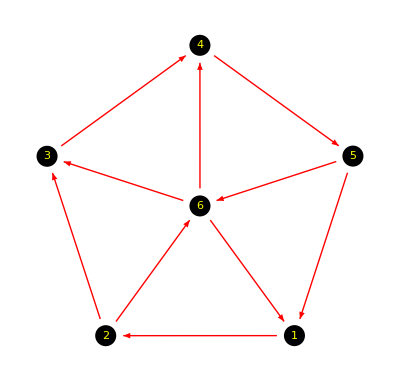

```mathematica
GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,.06],Yellow,Text[#2,#1]}&),EdgeRenderingFunction->({Red,Arrow[#1,0.1]}&),BaseStyle->{FontSize->12}]
```

#### Función 7.12. CAMINOS[]

```mathematica
CAMINOS[vertice1_,vertice2_,longitud_,matrizadyacencia_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[matrizadyacencia[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[matrizadyacencia][[1]]}];


If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud}];
caminostemp={};
Do[If[caminos[[k]][[longitud+1]]==vertice2,AppendTo[caminostemp,caminos[[k]]];];,{k,Length[caminos]}];
caminostemp
];
```

#### Ejemplo 7.7.

```mathematica
BC[n_,m_]:=Module[{i,j},
W=Table[i,{i,n+m}];
F={};
Do[Do[AppendTo[F,i->j],{i,n}];,{j,n+1,n+m}];
]
```

```mathematica
BC[3,4]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
matrizadyacencia=MATRIZADYACENCIA[W,F]
```

{{0,0,0,1,1,1,1},{0,0,0,1,1,1,1},{0,0,0,1,1,1,1},{1,1,1,0,0,0,0},{1,1,1,0,0,0,0},{1,1,1,0,0,0,0},{1,1,1,0,0,0,0}}

```mathematica
CAMINOS[vertice1_,vertice2_,longitud_,matrizadyacencia_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[matrizadyacencia[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[matrizadyacencia][[1]]}];


If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud}];
caminostemp={};
Do[If[caminos[[k]][[longitud+1]]==vertice2,AppendTo[caminostemp,caminos[[k]]];];,{k,Length[caminos]}];
caminostemp
];
```

```mathematica
caminos=CAMINOS[1,3,4,matrizadyacencia]
```

{{1,4,1,4,3},{1,4,1,5,3},{1,4,1,6,3},{1,4,1,7,3},{1,4,2,4,3},{1,4,2,5,3},{1,4,2,6,3},{1,4,2,7,3},{1,4,3,4,3},{1,4,3,5,3},{1,4,3,6,3},{1,4,3,7,3},{1,5,1,4,3},{1,5,1,5,3},{1,5,1,6,3},{1,5,1,7,3},{1,5,2,4,3},{1,5,2,5,3},{1,5,2,6,3},{1,5,2,7,3},{1,5,3,4,3},{1,5,3,5,3},{1,5,3,6,3},{1,5,3,7,3},{1,6,1,4,3},{1,6,1,5,3},{1,6,1,6,3},{1,6,1,7,3},{1,6,2,4,3},{1,6,2,5,3},{1,6,2,6,3},{1,6,2,7,3},{1,6,3,4,3},{1,6,3,5,3},{1,6,3,6,3},{1,6,3,7,3},{1,7,1,4,3},{1,7,1,5,3},{1,7,1,6,3},{1,7,1,7,3},{1,7,2,4,3},{1,7,2,5,3},{1,7,2,6,3},{1,7,2,7,3},{1,7,3,4,3},{1,7,3,5,3},{1,7,3,6,3},{1,7,3,7,3}}

```mathematica
Length[caminos]
```

48

```mathematica
MatrixPower[matrizadyacencia,4][[1,3]]
```

48

#### Ejemplo 7.8.

```mathematica
matrizadyacencia={{0,0,0,1,1},{1,0,0,1,0},{1,0,0,0,0},{0,0,1,0,1},{0,0,1,0,0}};
```

```mathematica
CAMINOS[vertice1_,vertice2_,longitud_,matrizadyacencia_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[matrizadyacencia[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[matrizadyacencia][[1]]}];


If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud}];
caminostemp={};
Do[If[caminos[[k]][[longitud+1]]==vertice2,AppendTo[caminostemp,caminos[[k]]];];,{k,Length[caminos]}];
caminostemp
];
```

```mathematica
caminos=CAMINOS[2,3,12,matrizadyacencia]
```

{{2,1,4,3,1,4,3,1,4,3,1,4,3},{2,1,4,3,1,4,3,1,4,3,1,5,3},{2,1,4,3,1,4,3,1,5,3,1,4,3},{2,1,4,3,1,4,3,1,5,3,1,5,3},{2,1,4,3,1,5,3,1,4,3,1,4,3},{2,1,4,3,1,5,3,1,4,3,1,5,3},{2,1,4,3,1,5,3,1,5,3,1,4,3},{2,1,4,3,1,5,3,1,5,3,1,5,3},{2,1,4,5,3,1,4,5,3,1,4,5,3},{2,1,5,3,1,4,3,1,4,3,1,4,3},{2,1,5,3,1,4,3,1,4,3,1,5,3},{2,1,5,3,1,4,3,1,5,3,1,4,3},{2,1,5,3,1,4,3,1,5,3,1,5,3},{2,1,5,3,1,5,3,1,4,3,1,4,3},{2,1,5,3,1,5,3,1,4,3,1,5,3},{2,1,5,3,1,5,3,1,5,3,1,4,3},{2,1,5,3,1,5,3,1,5,3,1,5,3},{2,4,3,1,4,3,1,4,3,1,4,5,3},{2,4,3,1,4,3,1,4,5,3,1,4,3},{2,4,3,1,4,3,1,4,5,3,1,5,3},{2,4,3,1,4,3,1,5,3,1,4,5,3},{2,4,3,1,4,5,3,1,4,3,1,4,3},{2,4,3,1,4,5,3,1,4,3,1,5,3},{2,4,3,1,4,5,3,1,5,3,1,4,3},{2,4,3,1,4,5,3,1,5,3,1,5,3},{2,4,3,1,5,3,1,4,3,1,4,5,3},{2,4,3,1,5,3,1,4,5,3,1,4,3},{2,4,3,1,5,3,1,4,5,3,1,5,3},{2,4,3,1,5,3,1,5,3,1,4,5,3},{2,4,5,3,1,4,3,1,4,3,1,4,3},{2,4,5,3,1,4,3,1,4,3,1,5,3},{2,4,5,3,1,4,3,1,5,3,1,4,3},{2,4,5,3,1,4,3,1,5,3,1,5,3},{2,4,5,3,1,5,3,1,4,3,1,4,3},{2,4,5,3,1,5,3,1,4,3,1,5,3},{2,4,5,3,1,5,3,1,5,3,1,4,3},{2,4,5,3,1,5,3,1,5,3,1,5,3}}

```mathematica
Length[caminos]==MatrixPower[matrizadyacencia,12][[2,3]]
```

True

## 3. GRAFOS CONEXOS Y COMPONENTES CONEXAS

### 3.1. GRAFOS CONEXOS. COMPONENTES CONEXAS

#### Función 7.13. CONEXO[]

```mathematica
CONEXO[A_]:=Module[{i,j,B},
   B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
   conexo=True;
   Do[
      Do[If[i!=j && B[[i,j]]==0,conexo=False;];
      ,{i,Dimensions[B][[1]]}];
   ,{j,Dimensions[B][[1]]}];     
conexo
]
```

#### Ejemplo 7.9.

```mathematica
CONEXO[A_]:=Module[{i,j,B},
   B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
   conexo=True;
   Do[
      Do[If[i!=j && B[[i,j]]==0,conexo=False;];
      ,{i,Dimensions[B][[1]]}];
   ,{j,Dimensions[B][[1]]}];     
conexo
]
```

```mathematica
CONEXO[matrizadyacencia=Table[If[i==j,0,1],{i,5},{j,5}]]
```

True

```mathematica
n=3;m=3;
A=Table[If[(i<=n &&j<=n)||(i>n &&j>n),0,1],{i,n+m},{j,n+m}]
CONEXO[A]
```

{{0,0,0,1,1,1},{0,0,0,1,1,1},{0,0,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,0},{1,1,1,0,0,0}}

True

```mathematica
<<Combinatorica`
```

```mathematica
ConnectedQ[FromAdjacencyMatrix[A]]
```

True

#### Ejemplo 7.10.

```mathematica
CONEXO[A_]:=Module[{i,j,B},
   B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
   conexo=True;
   Do[
      Do[If[i!=j && B[[i,j]]==0,conexo=False;];
      ,{i,Dimensions[B][[1]]}];
   ,{j,Dimensions[B][[1]]}];     
conexo
]
```

```mathematica
A={{0,1,0,0,0},{0,0,1,0,0},{1,0,0,0,0},{0,0,0,0,1},{0,0,0,0,0}};
```

```mathematica
A2=A+Transpose[A];
```

```mathematica
CONEXO[A2]
```

False

```mathematica
<<Combinatorica`
```

```mathematica
ConnectedQ[FromAdjacencyMatrix[A,Type->Directed],Weak]
```

False

#### Función 7.14. COMPONENTESCONEXAS[]

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
```

#### Ejemplo 7.11.

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
```

```mathematica
A={{0,1,1,0,0,0,0},{1,0,1,0,0,0,0},{1,1,0,0,0,0,0},{0,0,0,0,1,1,0},{0,0,0,1,0,1,0},{0,0,0,1,1,0,0},{0,0,0,0,0,0,0}};
COMPONENTESCONEXAS[A]
```

{{1,2,3},{4,5,6},{7}}

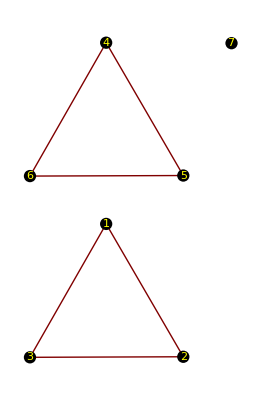

```mathematica
GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,.04],Yellow,Text[#2,#]}&),BaseStyle->{FontSize->12}]
```

```mathematica
<<GraphUtilities`;
```

```mathematica
WeakComponents[A]
```

{{1,2,3},{4,5,6},{7}}

```mathematica
<<Combinatorica`
```

```mathematica
ConnectedComponents[FromAdjacencyMatrix[A]]
```

{{1,2,3},{4,5,6},{7}}

#### Ejemplo 7.12.

```mathematica
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
```

```mathematica
A={{0,1,0,0,0},{0,0,1,0,0},{1,0,0,0,0},{0,0,0,0,1},{0,0,0,0,0}};
```

```mathematica
A2=A+Transpose[A];
```

```mathematica
COMPONENTESCONEXAS[A2]
```

{{1,2,3},{4,5}}

```mathematica
<<Combinatorica`
```

```mathematica
WeaklyConnectedComponents[FromAdjacencyMatrix[A,Type->Directed]]
```

{{1,2,3},{4,5}}

### 3.2. GRAFOS DIRIGIDOS FUERTEMENTE CONEXOS

```mathematica
FUERTEMENTECONEXO[A_]:=CONEXO[A];
```

#### Función 7.15. COMPONENTESFUERTEMENTECONEXAS[]

```mathematica
COMPONENTESFUERTEMENTECONEXAS[matrizadyacencia_]:=
   Module[{j,B,conjunto,temp,i},   
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];   
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto!={},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]!=0 && B[[conjunto[[i]],conjunto[[1]]]]!=0, AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];  
componentesconexas
]
```

#### Ejemplo 7.13.

```mathematica
A={{0,0,0,1,1},{1,0,0,1,0},{1,0,0,0,0},{0,0,1,0,1},{0,0,1,0,0}};
B={{0,1,0,0,1,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{1,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,1,1,0,0,1,0}};
```

```mathematica
COMPONENTESFUERTEMENTECONEXAS[matrizadyacencia_]:=
   Module[{j,B,conjunto,temp,i},   
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];   
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto!={},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]!=0 && B[[conjunto[[i]],conjunto[[1]]]]!=0, AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];  
componentesconexas
]
```

{{1,3,4,5},{2}}

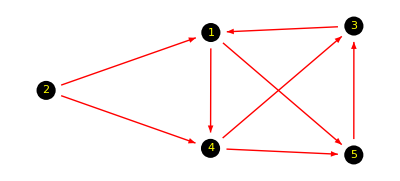

```mathematica
COMPONENTESFUERTEMENTECONEXAS[A]
GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,.06],Yellow,Text[#2,#1]}&),EdgeRenderingFunction->({Red,Arrow[#1,0.1]}&),BaseStyle->{FontSize->12}]
```

{{1,5,6},{2},{3},{4},{7},{8}}

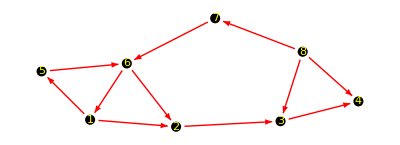

```mathematica
COMPONENTESFUERTEMENTECONEXAS[B]
GraphPlot[B,VertexRenderingFunction->({Black,Disk[#,.06],Yellow,Text[#2,#1]}&),EdgeRenderingFunction->({Red,Arrow[#1,0.1]}&),BaseStyle->{FontSize->10}]
```

```mathematica
<<GraphUtilities`;
```

```mathematica
StrongComponents[B]
```

{{4},{3},{2},{1,5,6},{7},{8}}

```mathematica
<<Combinatorica`
```

```mathematica
StronglyConnectedComponents[FromAdjacencyMatrix[B,Type->Directed]]
```

{{1,5,6},{2},{3},{4},{7},{8}}

## 4. DISTANCIAS Y GEODÉSICAS.CENTRO Y DIÁMETRO

#### Función 7.16. distancia[]

```mathematica
distancia[u_,v_,matrizadyacencia_]:=Module[{B},
n=1;
B=matrizadyacencia;
While[B[[u,v]]==0 && n<Dimensions[B][[1]],n++;B=MatrixPower[matrizadyacencia,n];];
If[n==Dimensions[B][[1]],Print["No están conectados"];,
Print[B[[u,v]]," geodésica/s. Distancia: ",n];];
]
```

#### Ejemplo 7.14.

```mathematica
B={{0,1,0,0,1,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{1,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,1,1,0,0,1,0}};
```

```mathematica
distancia[u_,v_,matrizadyacencia_]:=Module[{B},
n=1;
B=matrizadyacencia;
While[B[[u,v]]==0 && n<Dimensions[B][[1]],n++;B=MatrixPower[matrizadyacencia,n];];
If[n==Dimensions[B][[1]],Print["No están conectados"];,
Print[B[[u,v]]," geodésica/s. Distancia: ",n];];
]
```

```mathematica
distancia[1,3,B]
```

1 geodésica/s. Distancia: 2

```mathematica
distancia[8,2,B]
```

1 geodésica/s. Distancia: 3

```mathematica
distancia[8,1,B]
```

1 geodésica/s. Distancia: 3

```mathematica
distancia[1,8,B]
```

No están conectados

```mathematica
<<GraphUtilities`;
```

```mathematica
GraphDistance[B,3,1]
```

∞

#### Función 7.17. GEODESICAS[]

```mathematica
GEODESICAS[u_,v_,matrizadyacencia_]:=Module[{B},
n=1;
B=matrizadyacencia;
While[B[[u,v]]==0 && n<Dimensions[B][[1]],n++;B=MatrixPower[matrizadyacencia,n];];
If[n==Dimensions[B][[1]],Print["No están conectados"];,
Print[CAMINOS[u,v,n,matrizadyacencia]]];
]
```

#### Ejemplo 7.15.

```mathematica
BCadyacencia[n_,m_]:=Table[If[(i≤n &&j≤n)||(i>n &&j>n),0,1],{i,n+m},{j,n+m}];
```

```mathematica
A=BCadyacencia[3,4];
```

```mathematica
CAMINOS[vertice1_,vertice2_,longitud_,matrizadyacencia_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[matrizadyacencia[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[matrizadyacencia][[1]]}];


If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud}];
caminostemp={};
Do[If[caminos[[k]][[longitud+1]]==vertice2,AppendTo[caminostemp,caminos[[k]]];];,{k,Length[caminos]}];
caminostemp
];
```

```mathematica
GEODESICAS[u_,v_,matrizadyacencia_]:=Module[{B},
n=1;
B=matrizadyacencia;
While[B[[u,v]]==0 && n<Dimensions[B][[1]],n++;B=MatrixPower[matrizadyacencia,n];];
If[n==Dimensions[B][[1]],Print["No están conectados"];,
Print[CAMINOS[u,v,n,matrizadyacencia]]];
]
```

```mathematica
GEODESICAS[1,2,A]
```

{{1,4,2},{1,5,2},{1,6,2},{1,7,2}}

```mathematica
<<GraphUtilities`;
```

```mathematica
GraphPath[A,1,2]
```

{1,4,2}

```mathematica
<<Combinatorica`
```

```mathematica
ShortestPath[FromAdjacencyMatrix[A],1,2]
```

{1,7,2}

## 5. GRAFOS DE EULER

#### Función 7.18. EULER[]

```mathematica
EULER[matrizadyacencia_]:=Module[{A,i},
   Euler=True;
   If[CONEXO[matrizadyacencia],
      A=matrizadyacencia.matrizadyacencia;
      Do[
         If[Mod[A[[i,i]],2]==1,Euler=False;Break[];];
      ,{i,Length[matrizadyacencia]}];
   ,
      Euler=False;
   ];
   Euler
]
```

#### Función 7.19. EULERDIR[]

```mathematica
EULERDIR[matrizadyacencia_]:=Module[{i,grentrada,grsalida},
   Euler=True;
   If[FUERTEMENTECONEXO[matrizadyacencia],
      Do[
         grentrada=0;grsalida=0; 
         Do[
            If[matrizadyacencia[[i,j]]==1,grsalida++;];
            If[matrizadyacencia[[j,i]]==1,grentrada++;];
         ,{j,Length[matrizadyacencia]}];
          If[grentrada!=grsalida,Euler=False;Break[];];
      ,{i,Length[matrizadyacencia]}];
   ,
      Euler=False;
   ];
   Euler
]
```

#### Ejemplo 7.16.

```mathematica
CONEXO[A_]:=Module[{i,j,B},
   B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
   conexo=True;
   Do[
      Do[If[i!=j && B[[i,j]]==0,conexo=False;];
      ,{i,Dimensions[B][[1]]}];
   ,{j,Dimensions[B][[1]]}];     
conexo
]
```

```mathematica
EULER[matrizadyacencia_]:=Module[{A,i},
   Euler=True;
   If[CONEXO[matrizadyacencia],
      A=matrizadyacencia.matrizadyacencia;
      Do[
         If[Mod[A[[i,i]],2]==1,Euler=False;Break[];];
      ,{i,Length[matrizadyacencia]}];
   ,
      Euler=False;
   ];
   Euler
]
```

```mathematica
A1={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};
A2={{0,1,1,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{1,0,0,1,1,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,1,1,0,0,1},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,1,0,0,1,1,0}};
A3={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,1,0,0,0},{0,1,1,0,0,1,0,0,0,1,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,1,0,0,0,1,0,0,1,1,0},{0,0,0,1,0,0,0,1,1,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};
```

```mathematica
EULER[A1]
```

True

```mathematica
EULER[A2]
```

False

```mathematica
EULER[A3]
```

True

```mathematica
FUERTEMENTECONEXO[A_]:=CONEXO[A];
```

```mathematica
EULERDIR[matrizadyacencia_]:=Module[{i,grentrada,grsalida},
   Euler=True;
   If[FUERTEMENTECONEXO[matrizadyacencia],
      Do[
         grentrada=0;grsalida=0; 
         Do[
            If[matrizadyacencia[[i,j]]==1,grsalida++;];
            If[matrizadyacencia[[j,i]]==1,grentrada++;];
         ,{j,Length[matrizadyacencia]}];
          If[grentrada!=grsalida,Euler=False;Break[];];
      ,{i,Length[matrizadyacencia]}];
   ,
      Euler=False;
   ];
   Euler
]
```

```mathematica
A4={{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0}};
A5={{0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0}};
A6={{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0}};
```

```mathematica
EULERDIR[A4]
```

True

```mathematica
EULERDIR[A5]
```

False

```mathematica
EULERDIR[A6]
```

True

```mathematica
<<Combinatorica`
```

```mathematica
EulerianQ[FromAdjacencyMatrix[A1]]
EulerianQ[FromAdjacencyMatrix[A2]]
EulerianQ[FromAdjacencyMatrix[A3]]
EulerianQ[FromAdjacencyMatrix[A4,Type->Directed]]
EulerianQ[FromAdjacencyMatrix[A5,Type->Directed]]
EulerianQ[FromAdjacencyMatrix[A6,Type->Directed]]
```

True

False

True

True

False

True

#### Programa 7.20. Ciclo de Euler

F=CONJUNTO DE LADOS DE UN GRAFO NO ORIENTADO DE EULER;

tempF=F;
listaciclos={};
While[tempF≠{},
    camino={};
    inicio=tempF[[1,1]];
    otro=tempF[[1,2]];
    AppendTo[camino,tempF[[1,1]]];
    AppendTo[camino,tempF[[1,2]]];
    tempF=Complement[tempF,{tempF[[1]]}];
    While[otro≠inicio,
      j=1;
      ultimo=Last[camino];
      While[tempF[[j,1]]≠ultimo && tempF[[j,2]]≠ultimo ,j++];
      otro=Complement[{tempF[[j]][[1]],tempF[[j]][[2]]},{ultimo}][[1]];
      AppendTo[camino,otro];
      tempF=Complement[tempF,{tempF[[j]]}];
      ];
    AppendTo[listaciclos,camino];
    ];
nuevociclo=listaciclos[[1]];
While[Length[listaciclos]≠1,
    i=2;
    While[Intersection[listaciclos[[1]],listaciclos[[i]]]=={},i++];
    opcion=Intersection[listaciclos[[1]],listaciclos[[i]]][[1]];
    k1=Position[listaciclos[[1]],opcion][[1]][[1]];
    k2=Position[listaciclos[[i]],opcion][[1]][[1]];
    nuevociclo=listaciclos[[1]];
    t=1;
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,k2+1,Length[listaciclos[[i]]]}];
    Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,2,k2}];
    listaciclos=Delete[listaciclos,i];
    listaciclos=Delete[listaciclos,1];
    AppendTo[listaciclos,nuevociclo];
    ];
nuevociclo

#### Ejemplo 7.17.

```mathematica
A1={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};

A3={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,1,0,0,0},{0,1,1,0,0,1,0,0,0,1,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,1,0,0,0,1,0,0,1,1,0},{0,0,0,1,0,0,0,1,1,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};
```

```mathematica
matrizadyacencia=A1;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacencia][[1]]}];
```

```mathematica
tempF=F;
listaciclos={};
While[tempF≠{},
camino={};
inicio=tempF[[1,1]];
otro=tempF[[1,2]];
AppendTo[camino,tempF[[1,1]]];
AppendTo[camino,tempF[[1,2]]];
tempF=Complement[tempF,{tempF[[1]]}];
While[otro≠inicio,
j=1;
ultimo=Last[camino];
While[tempF[[j,1]]≠ultimo && tempF[[j,2]]≠ultimo ,j++];
otro=Complement[{tempF[[j]][[1]],tempF[[j]][[2]]},{ultimo}][[1]];
AppendTo[camino,otro];
tempF=Complement[tempF,{tempF[[j]]}];
];
AppendTo[listaciclos,camino];
];
nuevociclo=listaciclos[[1]];
While[Length[listaciclos]≠1,
i=2;
While[Intersection[listaciclos[[1]],listaciclos[[i]]]=={},i++];
opcion=Intersection[listaciclos[[1]],listaciclos[[i]]][[1]];
k1=Position[listaciclos[[1]],opcion][[1]][[1]];
k2=Position[listaciclos[[i]],opcion][[1]][[1]];
nuevociclo=listaciclos[[1]];
t=1;
Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,k2+1,Length[listaciclos[[i]]]}];
Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,2,k2}];
listaciclos=Delete[listaciclos,i];
listaciclos=Delete[listaciclos,1];
AppendTo[listaciclos,nuevociclo];
];
nuevociclo
```

{7,6,8,5,3,1,2,4,6,5,7,8,10,12,11,9,7}

```mathematica
matrizadyacencia=A3;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacencia][[1]]}];
```

```mathematica
tempF=F;
listaciclos={};
While[tempF≠{},
camino={};
inicio=tempF[[1,1]];
otro=tempF[[1,2]];
AppendTo[camino,tempF[[1,1]]];
AppendTo[camino,tempF[[1,2]]];
tempF=Complement[tempF,{tempF[[1]]}];
While[otro≠inicio,
j=1;
ultimo=Last[camino];
While[tempF[[j,1]]≠ultimo && tempF[[j,2]]≠ultimo ,j++];
otro=Complement[{tempF[[j]][[1]],tempF[[j]][[2]]},{ultimo}][[1]];
AppendTo[camino,otro];
tempF=Complement[tempF,{tempF[[j]]}];
];
AppendTo[listaciclos,camino];
];
nuevociclo=listaciclos[[1]];
While[Length[listaciclos]≠1,
i=2;
While[Intersection[listaciclos[[1]],listaciclos[[i]]]=={},i++];
opcion=Intersection[listaciclos[[1]],listaciclos[[i]]][[1]];
k1=Position[listaciclos[[1]],opcion][[1]][[1]];
k2=Position[listaciclos[[i]],opcion][[1]][[1]];
nuevociclo=listaciclos[[1]];
t=1;
Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,k2+1,Length[listaciclos[[i]]]}];
Do[nuevociclo=Insert[nuevociclo,listaciclos[[i]][[cont]],k1+t];t++;,{cont,2,k2}];
listaciclos=Delete[listaciclos,i];
listaciclos=Delete[listaciclos,1];
AppendTo[listaciclos,nuevociclo];
];
nuevociclo
```

{9,3,1,2,4,3,5,6,4,10,8,5,7,6,8,7,9,10,12,11,9}

```mathematica
<<Combinatorica`
```

```mathematica
EulerianCycle[FromAdjacencyMatrix[A1]]
EulerianCycle[FromAdjacencyMatrix[A3]]
```

{3,1,2,4,6,5,7,8,10,12,11,9,7,6,8,5,3}

{10,8,5,6,4,3,5,7,6,8,7,9,10,12,11,9,3,1,2,4,10}

#### Ejemplo 7.18.

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
nlados=21;
n=7;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

1.77636×10^-15. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 2 *************

DIVIDIMOS EN 2 CLASES

1.77636×10^-15. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 7 *************

DIVIDIMOS EN 5 CLASES

0.016. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 20 *************

DIVIDIMOS EN 10 CLASES

0.031. Total: 19

-------> Añadimos nuevo lado a 10 grafos

Van 1

************* DE 5 LADOS: 57 *************

DIVIDIMOS EN 21 CLASES

0.063. Total: 40

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 6 LADOS: 148 *************

DIVIDIMOS EN 41 CLASES

0.156. Total: 81

-------> Añadimos nuevo lado a 41 grafos

Van 1

************* DE 7 LADOS: 304 *************

DIVIDIMOS EN 65 CLASES

0.328. Total: 146

-------> Añadimos nuevo lado a 65 grafos

Van 1

************* DE 8 LADOS: 498 *************

DIVIDIMOS EN 97 CLASES

0.656. Total: 243

-------> Añadimos nuevo lado a 97 grafos

Van 1

************* DE 9 LADOS: 715 *************

DIVIDIMOS EN 131 CLASES

1.141. Total: 374

-------> Añadimos nuevo lado a 131 grafos

Van 1

Van 101

************* DE 10 LADOS: 897 *************

DIVIDIMOS EN 148 CLASES

1.844. Total: 522

-------> Añadimos nuevo lado a 148 grafos

Van 1

Van 101

************* DE 11 LADOS: 948 *************

DIVIDIMOS EN 148 CLASES

2.609. Total: 670

-------> Añadimos nuevo lado a 148 grafos

Van 1

Van 101

************* DE 12 LADOS: 850 *************

DIVIDIMOS EN 131 CLASES

3.266. Total: 801

-------> Añadimos nuevo lado a 131 grafos

Van 1

Van 101

************* DE 13 LADOS: 655 *************

DIVIDIMOS EN 97 CLASES

3.719. Total: 898

-------> Añadimos nuevo lado a 97 grafos

Van 1

************* DE 14 LADOS: 437 *************

DIVIDIMOS EN 65 CLASES

3.953. Total: 963

-------> Añadimos nuevo lado a 65 grafos

Van 1

************* DE 15 LADOS: 250 *************

DIVIDIMOS EN 41 CLASES

4.063. Total: 1004

-------> Añadimos nuevo lado a 41 grafos

Van 1

************* DE 16 LADOS: 118 *************

DIVIDIMOS EN 21 CLASES

4.125. Total: 1025

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 17 LADOS: 51 *************

DIVIDIMOS EN 10 CLASES

4.141. Total: 1035

-------> Añadimos nuevo lado a 10 grafos

Van 1

************* DE 18 LADOS: 17 *************

DIVIDIMOS EN 5 CLASES

4.141. Total: 1040

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 19 LADOS: 7 *************

DIVIDIMOS EN 2 CLASES

4.141. Total: 1042

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 20 LADOS: 2 *************

DIVIDIMOS EN 1 CLASES

4.156. Total: 1043

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 21 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

4.156. Total: 1044

Totales: 1044 Tiempo empleado: 4.156

96

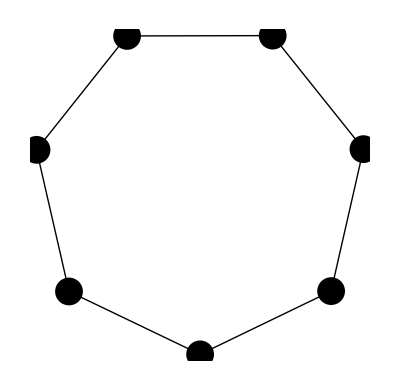

168

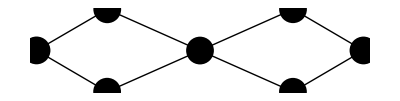

172

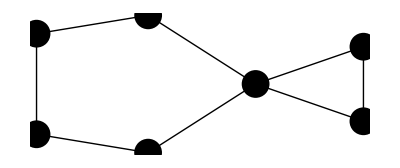

258

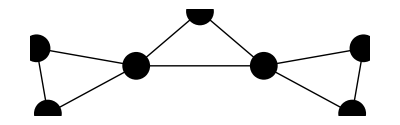

267

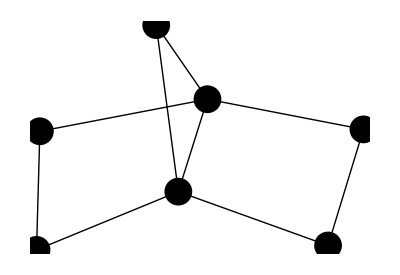

287

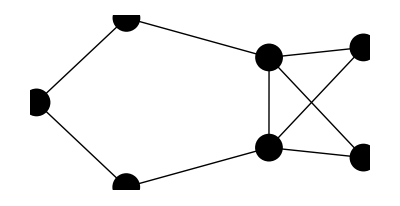

301

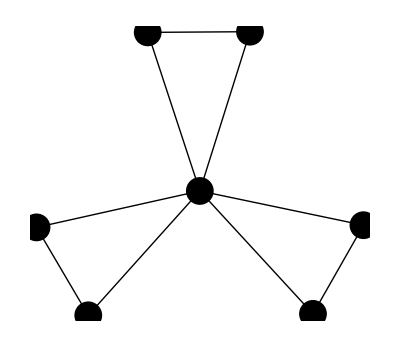

334

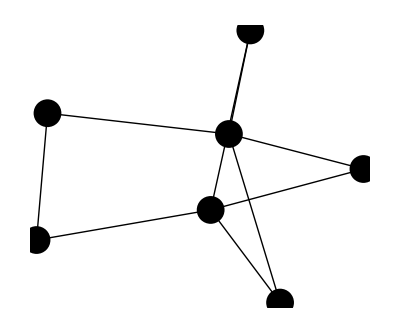

385

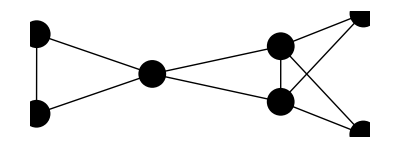

392

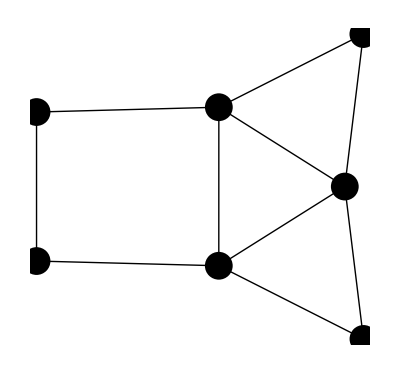

477

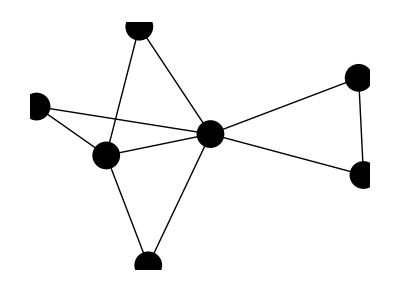

479

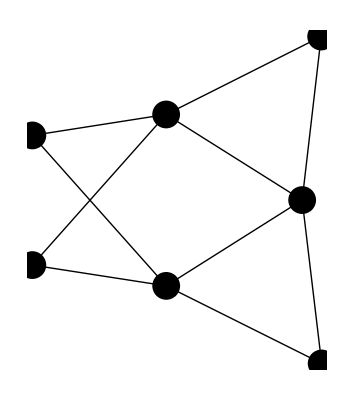

533

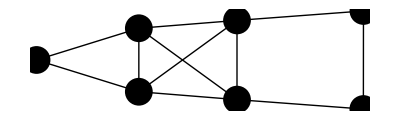

580

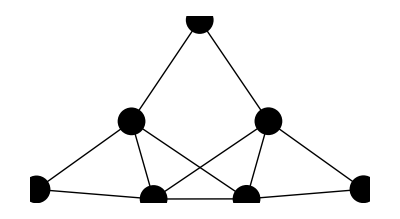

598

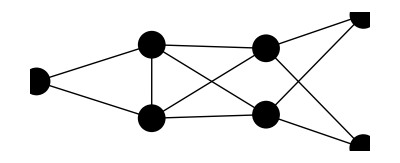

637

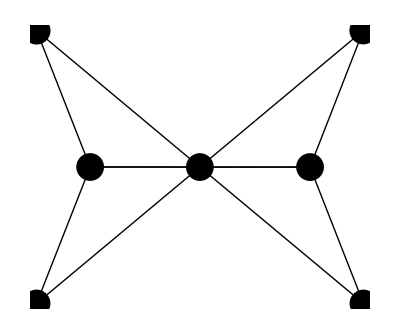

668

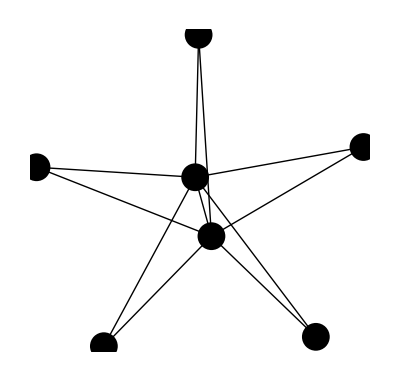

684

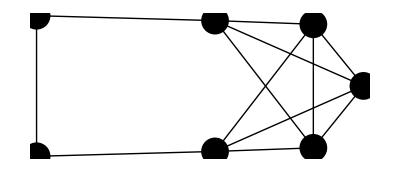

702

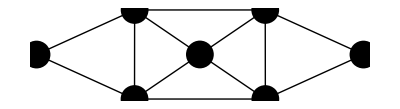

709

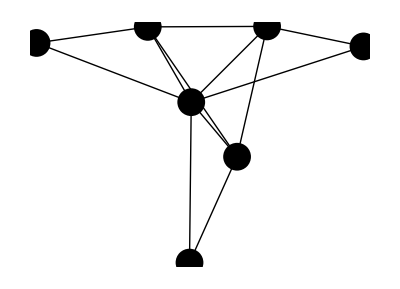

726

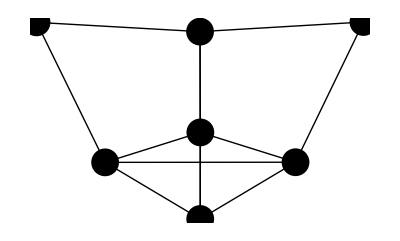

729

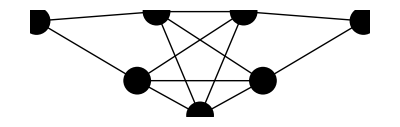

802

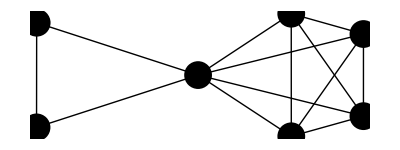

811

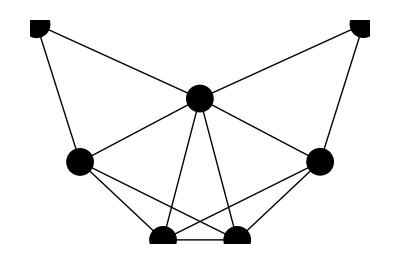

829

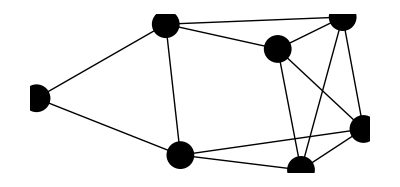

842

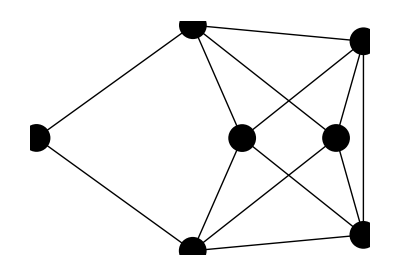

905

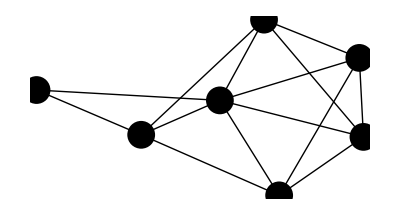

950

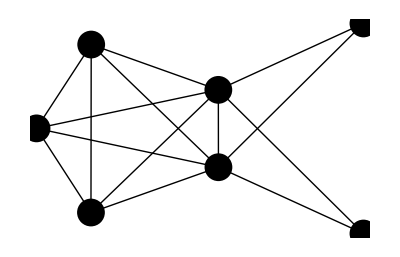

960

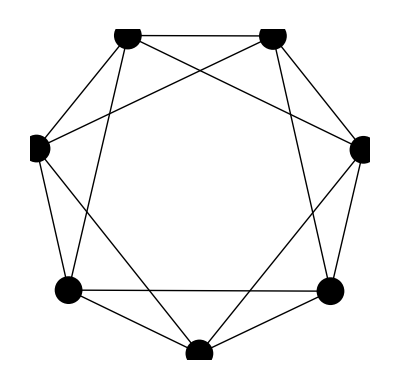

961

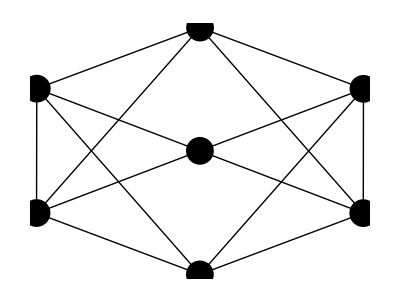

972

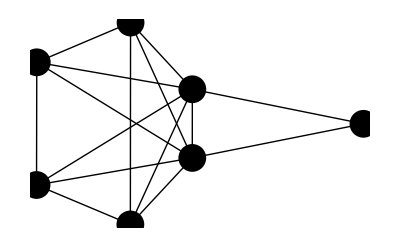

995

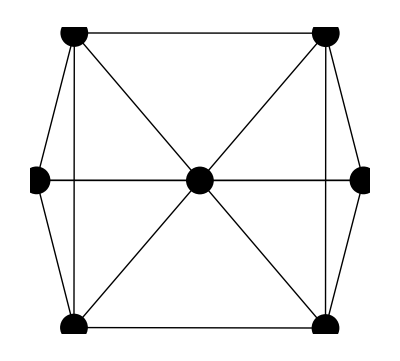

1002

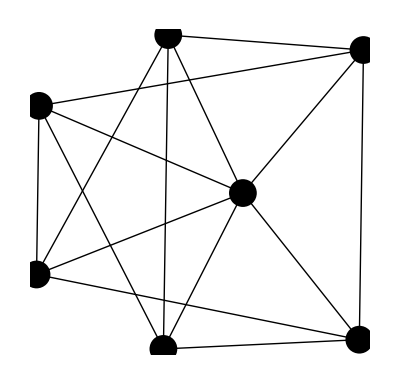

1021

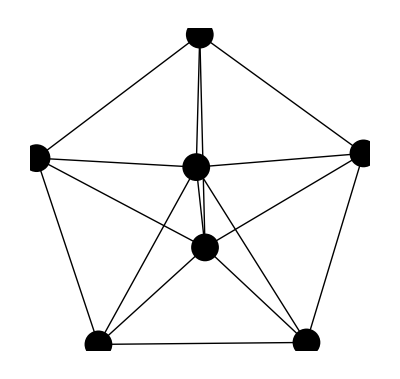

1030

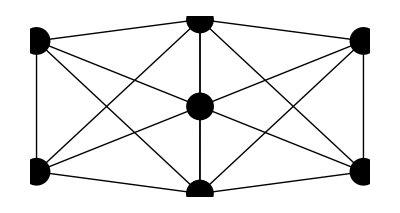

1038

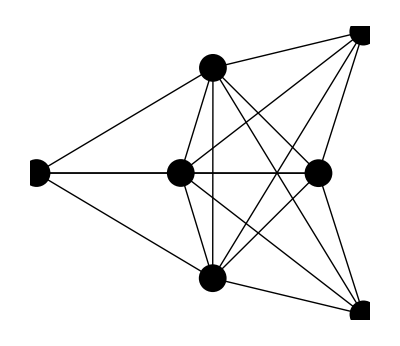

1044

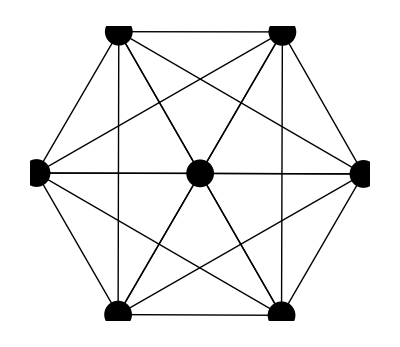

```mathematica
Do[
If[EULER[listamatrices1[[i]]]
,Print[i];
Print[GraphPlot[listamatrices1[[i]],PlotStyle->{Black,PointSize[.05]}]];
];
,{i,Length[listamatrices1]}]
```

## 6. GRAFOS DE HAMILTON

#### Función 7.21. HAMILTON[]

```mathematica
HAMILTON[A_]:=Module[{ciclos,adyacentes,ultvertice,ciclostemp,k,t,j,i},
ciclos={{1}};
Do[
ciclostemp={};
Do[
adyacentes={};

ultvertice=ciclos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,ciclos[[k]]];
If[adyacentes≠{},

Do[AppendTo[ciclostemp,Append[ciclos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[ciclos]}];
ciclos=ciclostemp;
,{i,Dimensions[A][[1]]-1}];
ciclostemp={};
Do[If[A[[1,ciclos[[k]][[Dimensions[A][[1]]]]]]==1,AppendTo[ciclostemp,Append[ciclos[[k]],1]];];,{k,Length[ciclos]}];
ciclostemp
];
```

#### Ejemplo 7.19.

```mathematica
HAMILTON[A_]:=Module[{ciclos,adyacentes,ultvertice,ciclostemp,k,t,j,i},
ciclos={{1}};
Do[
ciclostemp={};
Do[
adyacentes={};

ultvertice=ciclos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,ciclos[[k]]];
If[adyacentes≠{},

Do[AppendTo[ciclostemp,Append[ciclos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[ciclos]}];
ciclos=ciclostemp;
,{i,Dimensions[A][[1]]-1}];
ciclostemp={};
Do[If[A[[1,ciclos[[k]][[Dimensions[A][[1]]]]]]==1,AppendTo[ciclostemp,Append[ciclos[[k]],1]];];,{k,Length[ciclos]}];
ciclostemp
];
```

```mathematica
A1={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};
A2={{0,1,1,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{1,0,0,1,1,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,1,1,0,0,1},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,1,0,0,1,1,0}};
A3={{0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,1,0,0,0},{0,1,1,0,0,1,0,0,0,1,0,0},{0,0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,1,1,0,0,1,0,0},{0,0,1,0,0,0,1,0,0,1,1,0},{0,0,0,1,0,0,0,1,1,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,0}};
```

```mathematica
HAMILTON[A1]
```

{{1,2,4,6,7,9,11,12,10,8,5,3,1},{1,2,4,6,8,10,12,11,9,7,5,3,1},{1,3,5,7,9,11,12,10,8,6,4,2,1},{1,3,5,8,10,12,11,9,7,6,4,2,1}}

```mathematica
HAMILTON[A2]
```

{{1,2,4,6,8,10,12,11,9,7,5,3,1},{1,3,5,7,9,11,12,10,8,6,4,2,1}}

```mathematica
HAMILTON[A3]
```

{{1,2,4,6,5,7,8,10,12,11,9,3,1},{1,2,4,6,7,5,8,10,12,11,9,3,1},{1,2,4,6,7,9,11,12,10,8,5,3,1},{1,2,4,6,8,10,12,11,9,7,5,3,1},{1,2,4,10,12,11,9,7,6,8,5,3,1},{1,2,4,10,12,11,9,7,8,6,5,3,1},{1,3,5,6,8,7,9,11,12,10,4,2,1},{1,3,5,7,9,11,12,10,8,6,4,2,1},{1,3,5,8,6,7,9,11,12,10,4,2,1},{1,3,5,8,10,12,11,9,7,6,4,2,1},{1,3,9,11,12,10,8,5,7,6,4,2,1},{1,3,9,11,12,10,8,7,5,6,4,2,1}}

```mathematica
<<Combinatorica`
```

```mathematica
HamiltonianQ[FromAdjacencyMatrix[A1]]
HamiltonianCycle[FromAdjacencyMatrix[A2]]
HamiltonianCycle[FromAdjacencyMatrix[A3],All]
```

True

{1,2,4,6,8,10,12,11,9,7,5,3,1}

{{1,2,4,6,5,7,8,10,12,11,9,3,1},{1,2,4,6,7,5,8,10,12,11,9,3,1},{1,2,4,6,7,9,11,12,10,8,5,3,1},{1,2,4,6,8,10,12,11,9,7,5,3,1},{1,2,4,10,12,11,9,7,6,8,5,3,1},{1,2,4,10,12,11,9,7,8,6,5,3,1},{1,3,5,6,8,7,9,11,12,10,4,2,1},{1,3,5,7,9,11,12,10,8,6,4,2,1},{1,3,5,8,6,7,9,11,12,10,4,2,1},{1,3,5,8,10,12,11,9,7,6,4,2,1},{1,3,9,11,12,10,8,5,7,6,4,2,1},{1,3,9,11,12,10,8,7,5,6,4,2,1}}

#### Ejemplo 7.20.

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
nlados=15;
n=6;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.015. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 2 *************

DIVIDIMOS EN 2 CLASES

0.015. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 7 *************

DIVIDIMOS EN 5 CLASES

0.015. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 16 *************

DIVIDIMOS EN 9 CLASES

0.046. Total: 18

-------> Añadimos nuevo lado a 9 grafos

Van 1

************* DE 5 LADOS: 34 *************

DIVIDIMOS EN 15 CLASES

0.062. Total: 33

-------> Añadimos nuevo lado a 15 grafos

Van 1

************* DE 6 LADOS: 64 *************

DIVIDIMOS EN 21 CLASES

0.078. Total: 54

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 7 LADOS: 89 *************

DIVIDIMOS EN 24 CLASES

0.125. Total: 78

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 8 LADOS: 103 *************

DIVIDIMOS EN 24 CLASES

0.14. Total: 102

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 9 LADOS: 95 *************

DIVIDIMOS EN 21 CLASES

0.171. Total: 123

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 10 LADOS: 61 *************

DIVIDIMOS EN 15 CLASES

0.218. Total: 138

-------> Añadimos nuevo lado a 15 grafos

Van 1

************* DE 11 LADOS: 36 *************

DIVIDIMOS EN 9 CLASES

0.234. Total: 147

-------> Añadimos nuevo lado a 9 grafos

Van 1

************* DE 12 LADOS: 14 *************

DIVIDIMOS EN 5 CLASES

0.234. Total: 152

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 13 LADOS: 6 *************

DIVIDIMOS EN 2 CLASES

0.234. Total: 154

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 14 LADOS: 2 *************

DIVIDIMOS EN 1 CLASES

0.265. Total: 155

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 15 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.265. Total: 156

Totales: 156 Tiempo empleado: 0.265

34

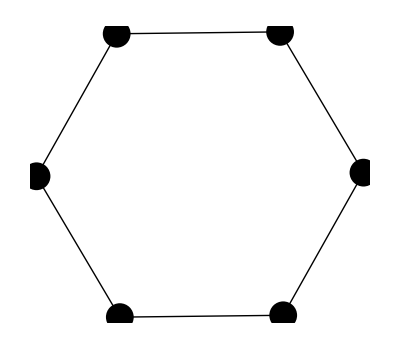

55

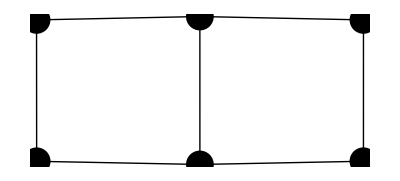

57

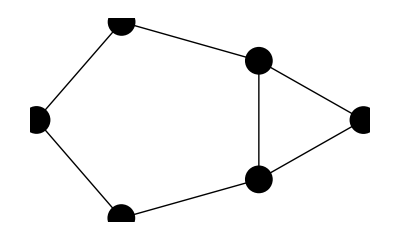

79

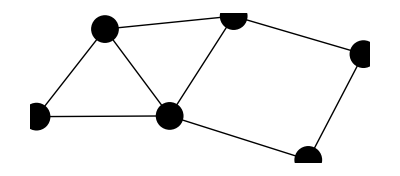

81

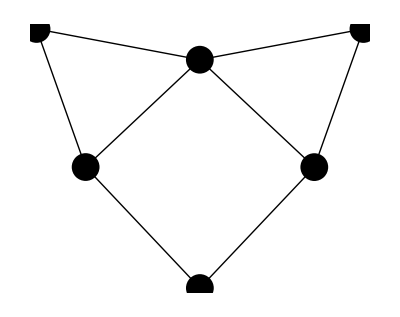

83

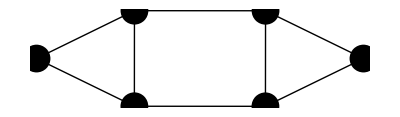

85

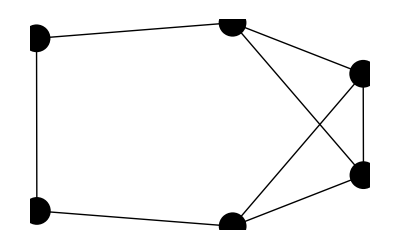

86

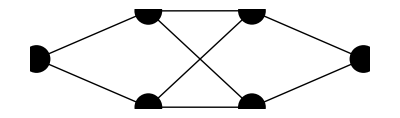

87

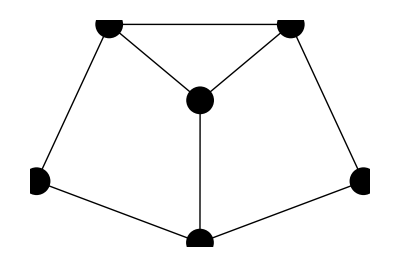

103

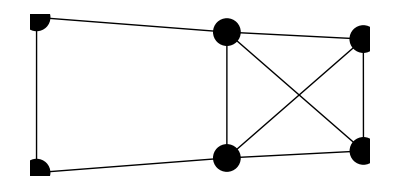

104

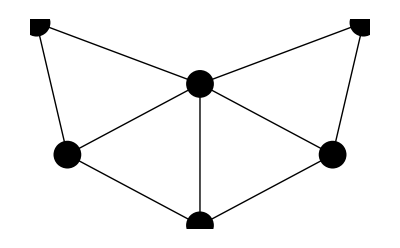

105

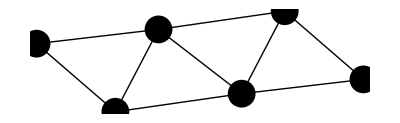

106

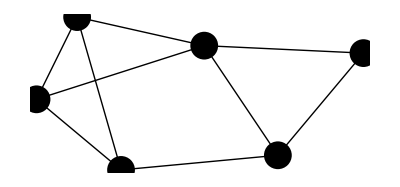

107

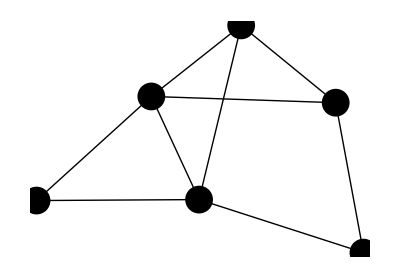

108

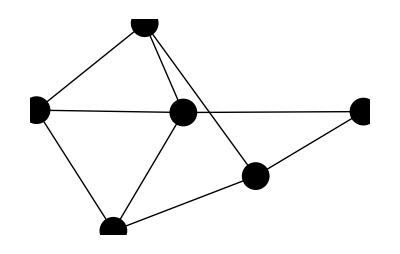

110

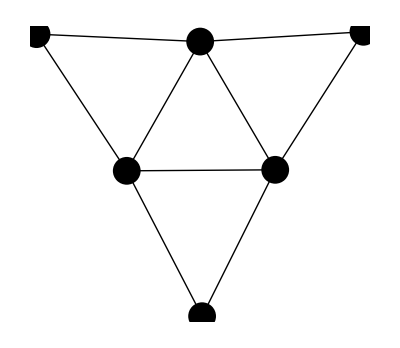

111

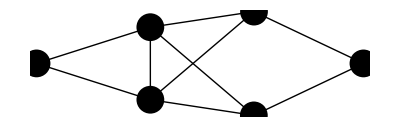

117

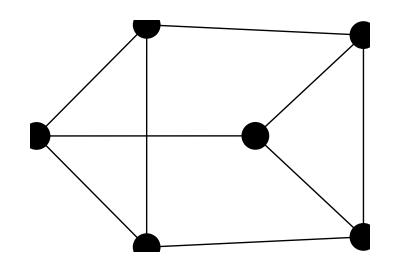

119

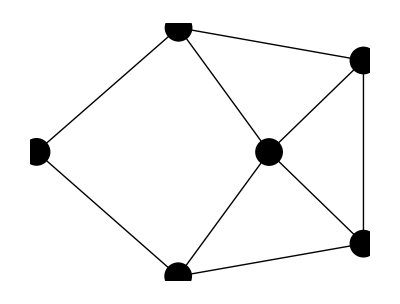

120

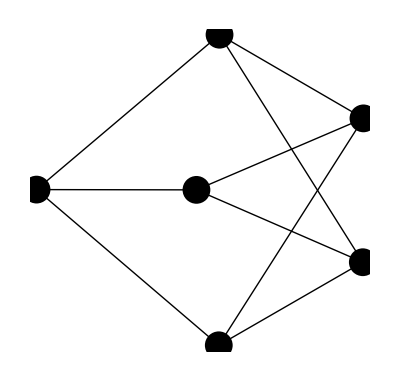

124

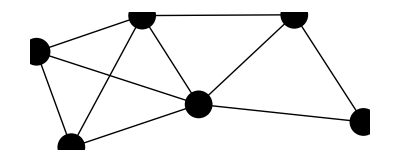

125

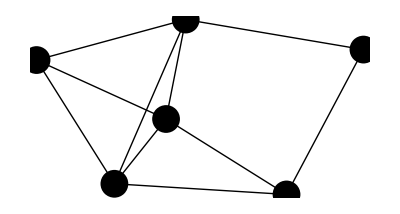

126

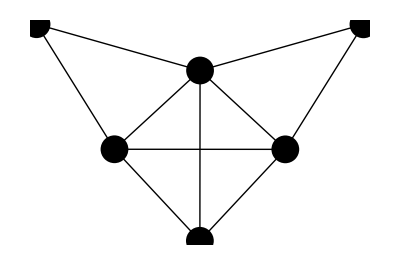

127

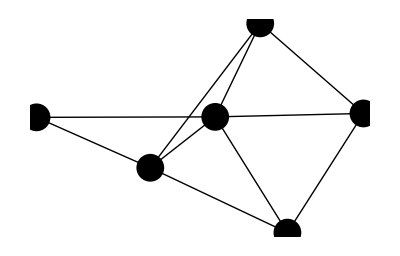

128

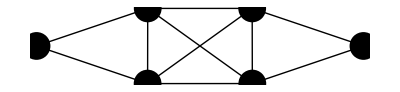

129

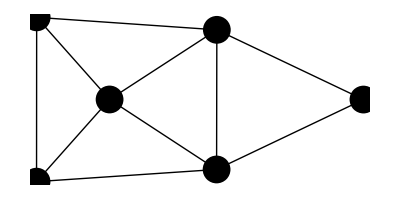

130

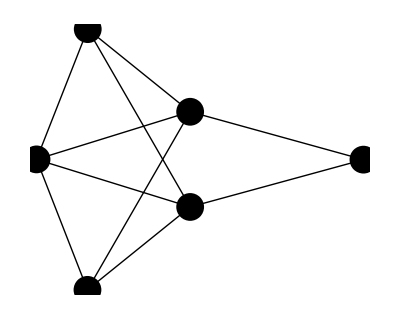

132

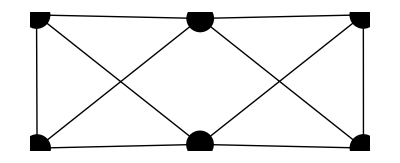

133

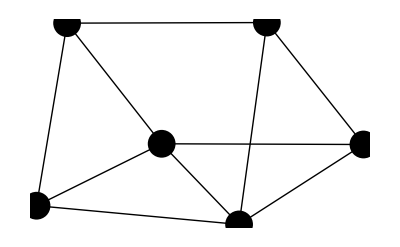

135

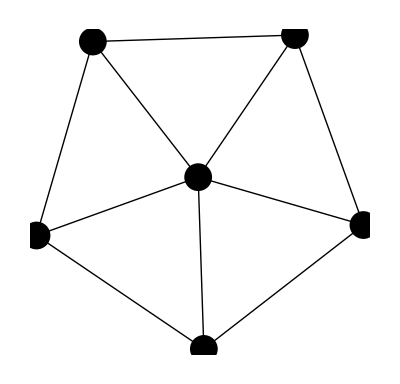

136

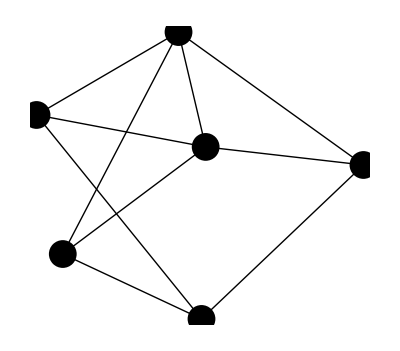

139

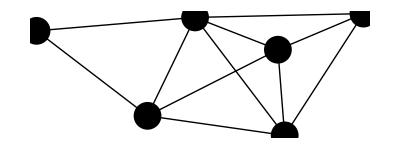

140

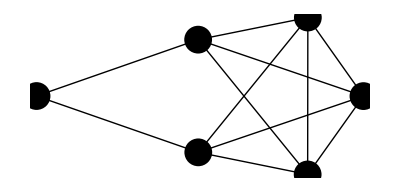

141

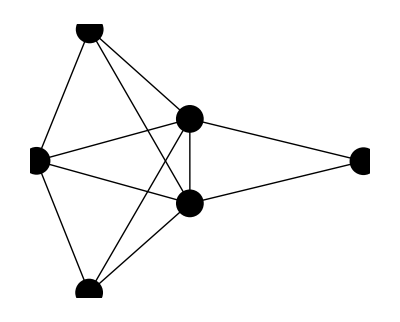

142

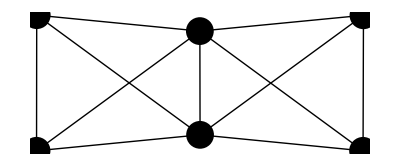

143

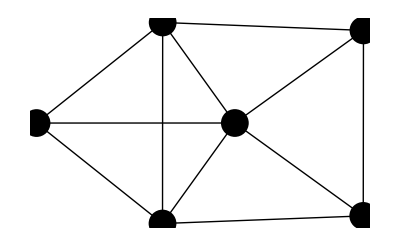

144

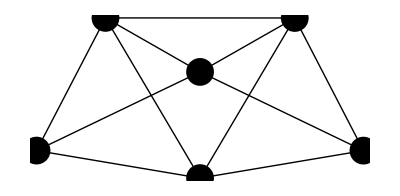

145

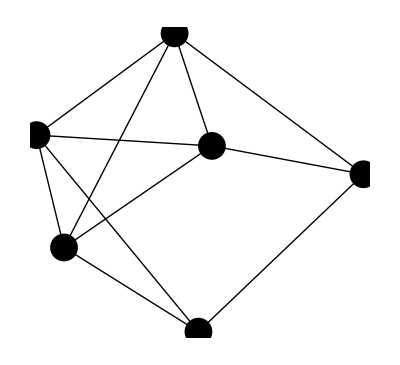

146

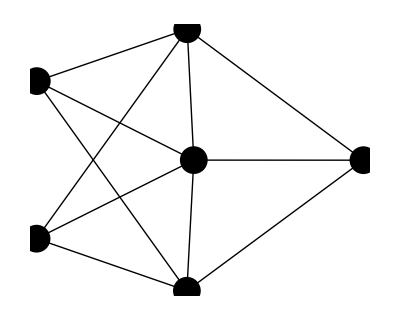

148

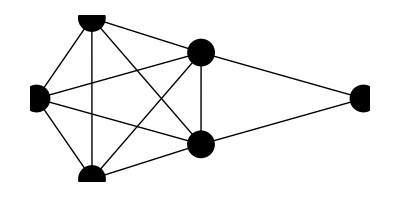

149

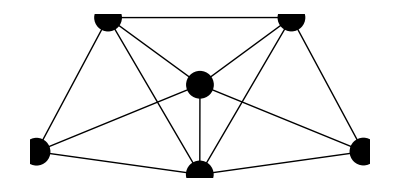

150

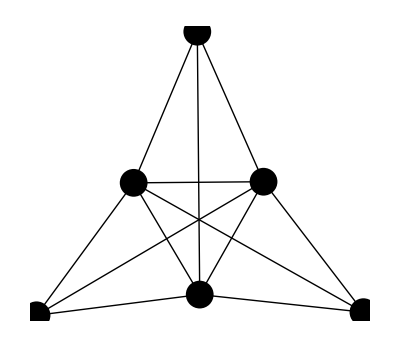

151

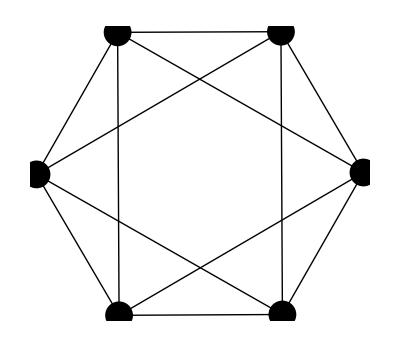

152

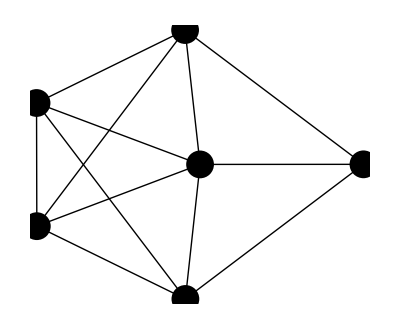

153

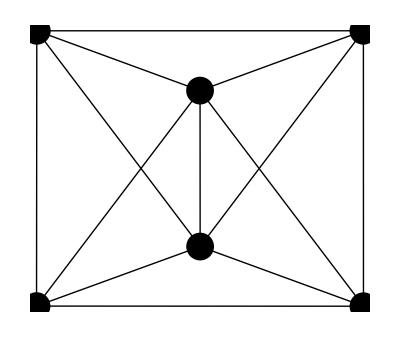

154

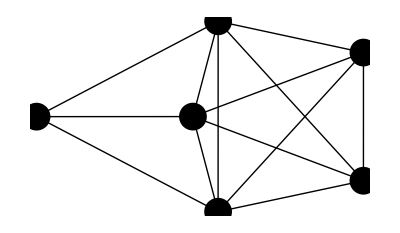

155

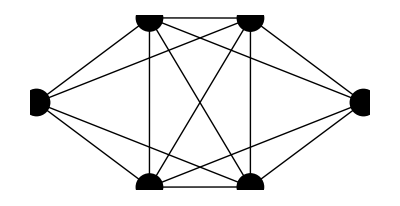

156

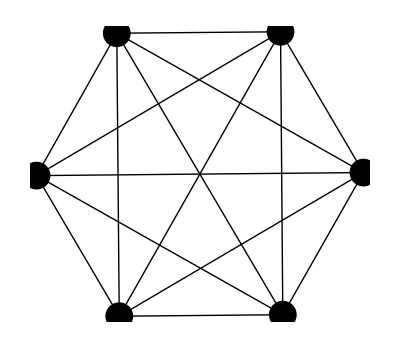

```mathematica
Do[
If[HAMILTON[listamatrices1[[i]]]≠{}
,Print[i];
Print[GraphPlot[listamatrices1[[i]],PlotStyle->{Black,PointSize[.05]}]];
];
,{i,Length[listamatrices1]}]
```

## 8. OTROS EJEMPLOS

#### Ejemplo 7.21.

```mathematica
HAMILTON[A_]:=Module[{ciclos,adyacentes,ultvertice,ciclostemp,k,t,j,i},
ciclos={{1}};
Do[
ciclostemp={};
Do[
adyacentes={};

ultvertice=ciclos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,ciclos[[k]]];
If[adyacentes≠{},

Do[AppendTo[ciclostemp,Append[ciclos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[ciclos]}];
ciclos=ciclostemp;
,{i,Dimensions[A][[1]]-1}];
ciclostemp={};
Do[If[A[[1,ciclos[[k]][[Dimensions[A][[1]]]]]]==1,AppendTo[ciclostemp,Append[ciclos[[k]],1]];];,{k,Length[ciclos]}];
ciclostemp
];
```

```mathematica
A={{0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},
{0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0},
{1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0}};
```

```mathematica
Timing[hamilton=HAMILTON[A]]
```

{0.953,{{1,2,5,4,3,6,7,8,9,10,15,18,20,19,17,14,13,16,12,11,1},{1,2,5,4,3,6,12,16,19,17,14,13,7,8,9,10,15,18,20,11,1},{1,2,5,4,8,7,13,16,19,17,14,9,10,15,18,20,11,12,6,3,1},{1,2,5,4,8,9,10,15,18,20,11,12,16,19,17,14,13,7,6,3,1},{1,2,5,10,9,8,4,3,6,7,13,14,17,15,18,20,19,16,12,11,1},{1,2,5,10,9,14,13,7,8,4,3,6,12,16,19,17,15,18,20,11,1},{1,2,5,10,9,14,13,16,19,17,15,18,20,11,12,6,7,8,4,3,1},{1,2,5,10,9,14,17,15,18,20,19,16,13,7,8,4,3,6,12,11,1},{1,2,5,10,15,18,20,11,12,6,7,13,16,19,17,14,9,8,4,3,1},{1,2,5,10,15,18,20,19,17,14,9,8,4,3,6,7,13,16,12,11,1},{1,2,18,15,10,5,4,3,6,12,16,13,7,8,9,14,17,19,20,11,1},{1,2,18,15,10,5,4,8,9,14,17,19,20,11,12,16,13,7,6,3,1},{1,2,18,15,17,14,9,10,5,4,8,7,13,16,19,20,11,12,6,3,1},{1,2,18,15,17,14,13,7,8,9,10,5,4,3,6,12,16,19,20,11,1},{1,2,18,15,17,14,13,16,19,20,11,12,6,7,8,9,10,5,4,3,1},{1,2,18,15,17,19,20,11,12,16,13,14,9,10,5,4,8,7,6,3,1},{1,2,18,20,11,12,6,7,8,9,14,13,16,19,17,15,10,5,4,3,1},{1,2,18,20,11,12,16,19,17,15,10,5,4,8,9,14,13,7,6,3,1},{1,2,18,20,19,16,13,7,8,9,14,17,15,10,5,4,3,6,12,11,1},{1,2,18,20,19,17,15,10,5,4,3,6,7,8,9,14,13,16,12,11,1},{1,3,4,5,2,18,15,10,9,8,7,6,12,16,13,14,17,19,20,11,1},{1,3,4,5,2,18,20,19,16,13,14,17,15,10,9,8,7,6,12,11,1},{1,3,4,5,10,9,8,7,6,12,11,20,19,16,13,14,17,15,18,2,1},{1,3,4,5,10,15,17,19,16,13,14,9,8,7,6,12,11,20,18,2,1},{1,3,4,8,7,6,12,11,20,18,15,17,19,16,13,14,9,10,5,2,1},{1,3,4,8,7,6,12,16,13,14,9,10,5,2,18,15,17,19,20,11,1},{1,3,4,8,9,10,5,2,18,15,17,14,13,7,6,12,16,19,20,11,1},{1,3,4,8,9,14,13,7,6,12,16,19,17,15,10,5,2,18,20,11,1},{1,3,4,8,9,14,17,15,10,5,2,18,20,19,16,13,7,6,12,11,1},{1,3,4,8,9,14,17,19,16,13,7,6,12,11,20,18,15,10,5,2,1},{1,3,6,7,8,4,5,2,18,20,19,17,15,10,9,14,13,16,12,11,1},{1,3,6,7,8,4,5,10,9,14,13,16,12,11,20,19,17,15,18,2,1},{1,3,6,7,13,14,9,8,4,5,10,15,17,19,16,12,11,20,18,2,1},{1,3,6,7,13,14,17,15,10,9,8,4,5,2,18,20,19,16,12,11,1},{1,3,6,7,13,14,17,19,16,12,11,20,18,15,10,9,8,4,5,2,1},{1,3,6,7,13,16,12,11,20,19,17,14,9,8,4,5,10,15,18,2,1},{1,3,6,12,11,20,18,15,10,9,14,17,19,16,13,7,8,4,5,2,1},{1,3,6,12,11,20,19,16,13,7,8,4,5,10,9,14,17,15,18,2,1},{1,3,6,12,16,13,7,8,4,5,2,18,15,10,9,14,17,19,20,11,1},{1,3,6,12,16,19,17,15,10,9,14,13,7,8,4,5,2,18,20,11,1},{1,11,12,6,3,4,5,10,15,17,14,9,8,7,13,16,19,20,18,2,1},{1,11,12,6,3,4,8,7,13,16,19,20,18,15,17,14,9,10,5,2,1},{1,11,12,6,7,8,9,10,15,17,14,13,16,19,20,18,2,5,4,3,1},{1,11,12,6,7,13,16,19,20,18,2,5,10,15,17,14,9,8,4,3,1},{1,11,12,16,13,7,6,3,4,8,9,14,17,19,20,18,15,10,5,2,1},{1,11,12,16,13,14,9,8,7,6,3,4,5,10,15,17,19,20,18,2,1},{1,11,12,16,13,14,9,10,15,17,19,20,18,2,5,4,8,7,6,3,1},{1,11,12,16,13,14,17,19,20,18,15,10,9,8,7,6,3,4,5,2,1},{1,11,12,16,19,20,18,2,5,4,8,9,10,15,17,14,13,7,6,3,1},{1,11,12,16,19,20,18,15,17,14,13,7,6,3,4,8,9,10,5,2,1},{1,11,20,18,2,5,4,8,7,13,14,9,10,15,17,19,16,12,6,3,1},{1,11,20,18,2,5,10,15,17,19,16,12,6,7,13,14,9,8,4,3,1},{1,11,20,18,15,10,9,8,7,13,14,17,19,16,12,6,3,4,5,2,1},{1,11,20,18,15,17,19,16,12,6,3,4,8,7,13,14,9,10,5,2,1},{1,11,20,19,16,12,6,3,4,5,10,9,8,7,13,14,17,15,18,2,1},{1,11,20,19,16,12,6,7,13,14,17,15,18,2,5,10,9,8,4,3,1},{1,11,20,19,17,14,9,8,7,13,16,12,6,3,4,5,10,15,18,2,1},{1,11,20,19,17,14,9,10,15,18,2,5,4,8,7,13,16,12,6,3,1},{1,11,20,19,17,14,13,16,12,6,7,8,9,10,15,18,2,5,4,3,1},{1,11,20,19,17,15,18,2,5,10,9,14,13,16,12,6,7,8,4,3,1}}}

```mathematica
Length[hamilton]
```

60

```mathematica
hamilton2={hamilton[[1]]};
Do[
caminoinv=Table[hamilton[[CONTADORi]][[21-i]],{i,0,20}];
If[Intersection[hamilton2,{caminoinv}]=={},AppendTo[hamilton2,hamilton[[CONTADORi]]];];
,{CONTADORi, 2,Length[hamilton]}]
hamilton=hamilton2;
```

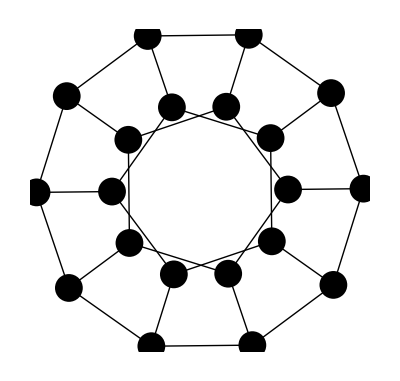

```mathematica
GraphPlot[A,PlotStyle->{Black,PointSize[.05]}]
```

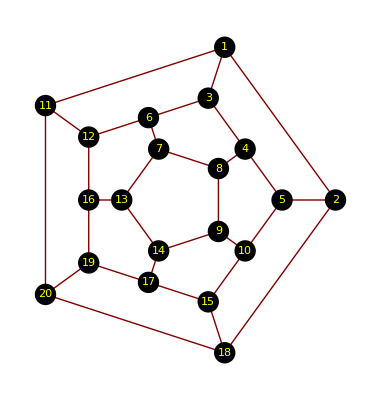

```mathematica
coordenadas=Table[{0,0},{i,20}];
coordenadas[[1]]={Cos[1/5*2*Pi]*3,Sin[1/5*2*Pi]*3};
coordenadas[[11]]={Cos[2/5*2*Pi]*3,Sin[2/5*2*Pi]*3};
coordenadas[[20]]={Cos[3/5*2*Pi]*3,Sin[3/5*2*Pi]*3};
coordenadas[[18]]={Cos[4/5*2*Pi]*3,Sin[4/5*2*Pi]*3};
coordenadas[[2]]={Cos[2*Pi]*3,Sin[2*Pi]*3};
coordenadas[[3]]={Cos[1/5*2*Pi]*2,Sin[1/5*2*Pi]*2};
coordenadas[[12]]={Cos[2/5*2*Pi]*2,Sin[2/5*2*Pi]*2};
coordenadas[[19]]={Cos[3/5*2*Pi]*2,Sin[3/5*2*Pi]*2};
coordenadas[[15]]={Cos[4/5*2*Pi]*2,Sin[4/5*2*Pi]*2};
coordenadas[[5]]={Cos[2*Pi]*2,Sin[2*Pi]*2};
coordenadas[[7]]={Cos[15/50*2*Pi],Sin[15/50*2*Pi]};
coordenadas[[13]]={Cos[25/50*2*Pi],Sin[25/50*2*Pi]};
coordenadas[[14]]={Cos[35/50*2*Pi],Sin[35/50*2*Pi]};
coordenadas[[9]]={Cos[45/50*2*Pi],Sin[45/50*2*Pi]};
coordenadas[[8]]={Cos[55/50*2*Pi],Sin[55/50*2*Pi]};
coordenadas[[4]]={(coordenadas[[3]][[1]]+coordenadas[[5]][[1]])/2,(coordenadas[[3]][[2]]+coordenadas[[5]][[2]])/2};
coordenadas[[6]]={(coordenadas[[3]][[1]]+coordenadas[[12]][[1]])/2,(coordenadas[[3]][[2]]+coordenadas[[12]][[2]])/2};
coordenadas[[10]]={(coordenadas[[15]][[1]]+coordenadas[[5]][[1]])/2,(coordenadas[[15]][[2]]+coordenadas[[5]][[2]])/2};
coordenadas[[16]]={(coordenadas[[12]][[1]]+coordenadas[[19]][[1]])/2,(coordenadas[[12]][[2]]+coordenadas[[19]][[2]])/2};
coordenadas[[17]]={(coordenadas[[15]][[1]]+coordenadas[[19]][[1]])/2,(coordenadas[[15]][[2]]+coordenadas[[19]][[2]])/2};
GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,.2],Yellow,Text[#2,#1]}&),VertexCoordinateRules->coordenadas]
```

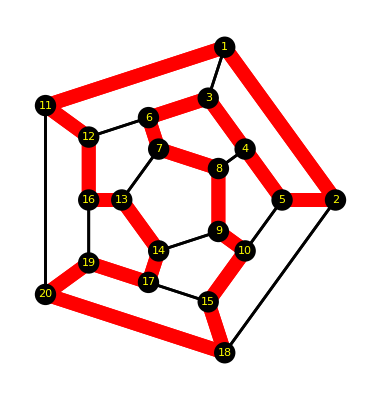

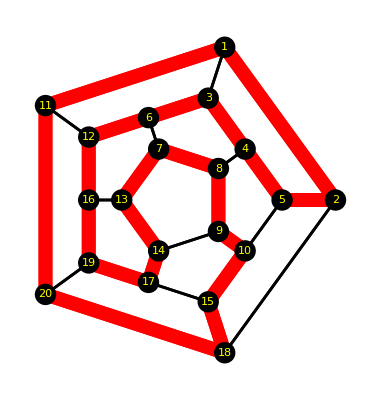

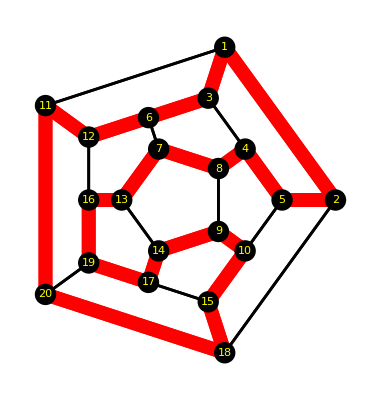

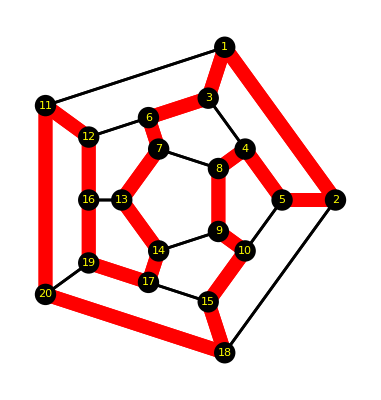

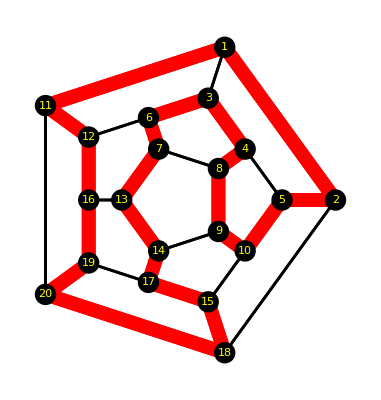

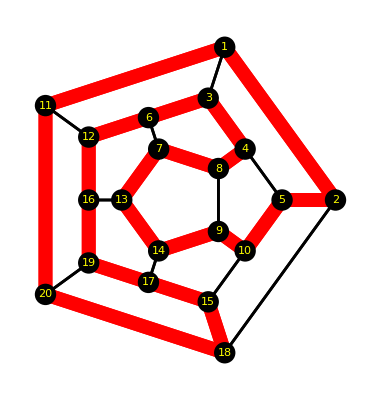

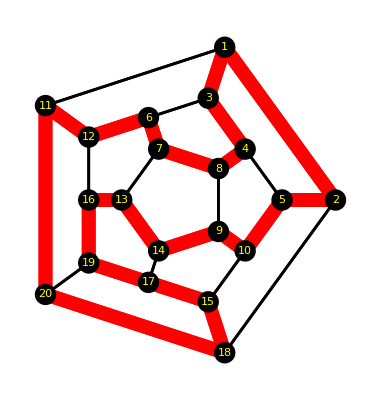

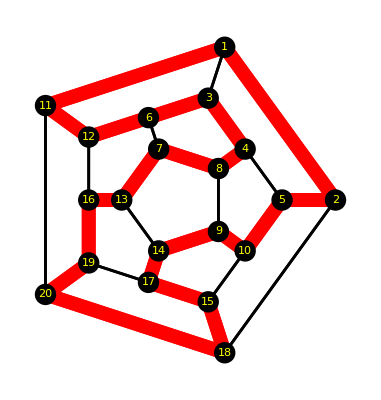

```mathematica
W=Table[i,{i,Dimensions[A][[1]]}];
F={};
Do[Do[If[A[[i,j]]==1,AppendTo[F,Sort[{i,j}]]];,{i,j}];,{j,Dimensions[A][[1]]}];

Do[
camino=Table[Sort[{hamilton[[CONTADORj]][[i]],hamilton[[CONTADORj]][[i+1]]}],{i,Length[hamilton[[CONTADORj]]]-1}];
Do[
If[Intersection[camino,{F[[CONTADORi]]}]=={},
colores[F[[CONTADORi]]]=Black;
grosor[F[[CONTADORi]]]=0.005;,
colores[F[[CONTADORi]]]=Red;
grosor[F[[CONTADORi]]]=0.025;
];
,{CONTADORi,Length[F]}];
Print[GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,.2],Yellow,Text[#2,#1]}&),VertexCoordinateRules->coordenadas,EdgeRenderingFunction->Function[{i,j},{colores[Sort[j]],Thickness[grosor[Sort[j]]],Line[i]}]]];
,{CONTADORj,Length[hamilton]}];
```

```mathematica
<<Combinatorica`
```

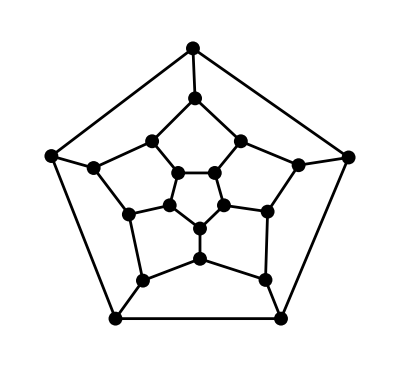

```mathematica
ShowGraph[DodecahedralGraph]
```

```mathematica
IsomorphicQ[FromAdjacencyMatrix[A],DodecahedralGraph]
```

True

```mathematica
Timing[Length[HamiltonianCycle[DodecahedralGraph,All]]]
```

{2.969,60}

#### Ejemplo 7.22.

```mathematica
W={a,b,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25};
F={a->1,a->2,a->3,2->4,1->5,2->5,5->6,5->7,7->8,7->9,7->3,3->10,10->22,10->11,11->12,11->13,13->25,13->14,14->15,15->16,13->18,18->20,20->21,20->17,17->19,17->23,23->24,23->b};
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
A=MATRIZADYACENCIA[W,F];
```

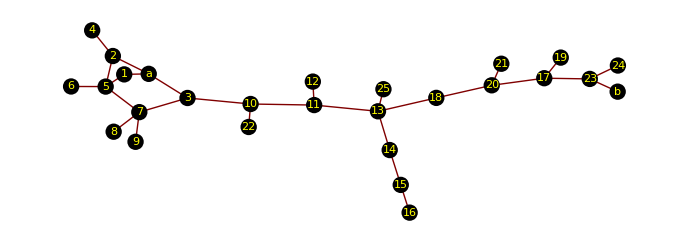

```mathematica
GraphPlot[F,VertexRenderingFunction->({Black,Disk[#,.2],Yellow,Text[#2,#]}&)]
```

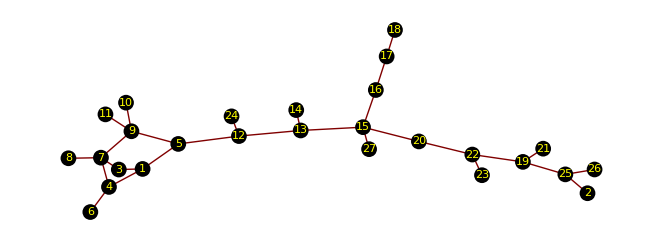

```mathematica
GraphPlot[A,VertexRenderingFunction->({Black,Disk[#,.2],Yellow,Text[#2,#]}&)]
```

```mathematica
GEODESICAS[u_, v_, matrizadyacencia_] := Module[{B},
  n = 1;
  B = matrizadyacencia;
  While[B[[u, v]] == 0 && n < Dimensions[B][[1]], n++; B = MatrixPower[matrizadyacencia, n];];
  If[n == Dimensions[B][[1]], Print["No están conectados"];,
   Print[CAMINOS[u, v, n, matrizadyacencia]]];
  ]
```

```mathematica
CAMINOS[vertice1_,vertice2_,longitud_,matrizadyacencia_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[matrizadyacencia[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[matrizadyacencia][[1]]}];


If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud}];
caminostemp={};
Do[If[caminos[[k]][[longitud+1]]==vertice2,AppendTo[caminostemp,caminos[[k]]];];,{k,Length[caminos]}];
caminostemp
];
```

```mathematica
GEODESICAS[1,2,A]
```

{{1,5,12,13,15,20,22,19,25,2}}

```mathematica
geo={1,5,12,13,15,20,22,19,25,2};
Table[W[[geo[[i]]]],{i,Length[geo]}]
```

{a,3,10,11,13,18,20,17,23,b}

#### Ejemplo 7.23.

```mathematica
<<Combinatorica`
```

```mathematica
grafos={TetrahedralGraph,OctahedralGraph,CubicalGraph,IcosahedralGraph,DodecahedralGraph,Hypercube[4]};
```

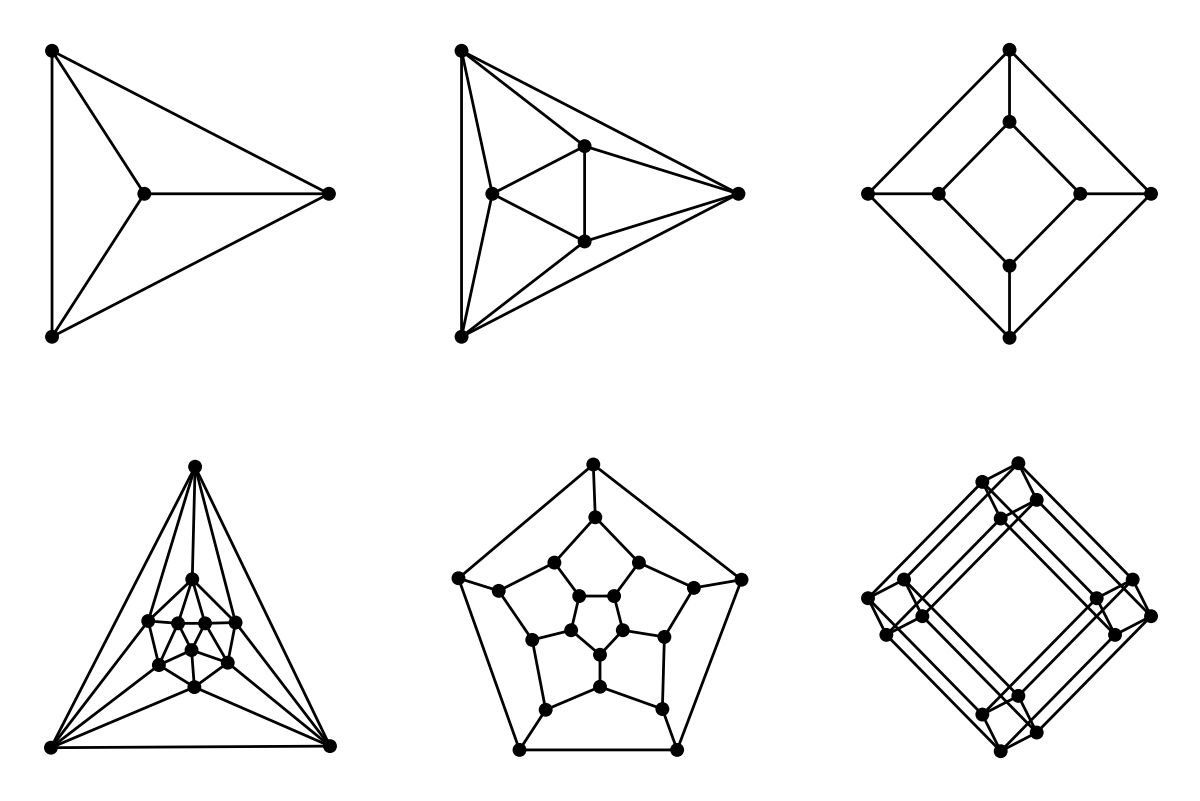

```mathematica
ShowGraphArray[{grafos[[1;;3]],grafos[[4;;6]]}]
```

```mathematica
Do[Print[i,"   Euler: ",EulerianQ[grafos[[i]]],"   Hamilton: ",HamiltonianQ[grafos[[i]]]],{i,Length[grafos]}];
```

1   Euler: False   Hamilton: True

2   Euler: True   Hamilton: True

3   Euler: False   Hamilton: True

4   Euler: False   Hamilton: True

5   Euler: False   Hamilton: True

6   Euler: True   Hamilton: True

```mathematica
grafo=OctahedralGraph;
camino=EulerianCycle[grafo];
lados=Edges[grafo];
Do[
ciclo=camino[[1;;k+1]];
ladosciclo=Table[Sort[{ciclo[[i]],ciclo[[i+1]]}],{i,Length[ciclo]-1}];
Do[
If[Intersection[{Sort[lados[[i]]]},ladosciclo]=={},
color[Sort[lados[[i]]]]=Yellow;
grosor[Sort[lados[[i]]]]=.02;
,
color[Sort[lados[[i]]]]=Red;
grosor[Sort[lados[[i]]]]=.04;
];
,{i,Length[lados]}];

framegrafo[k]=GraphPlot3D[ToAdjacencyMatrix[grafo],VertexRenderingFunction->({Blue,Sphere[#,.1],White,Text[#2,#1]}&),EdgeRenderingFunction->Function[{i,j},{color[Sort[j]],Cylinder[i,grosor[Sort[j]]]}]];

,{k,Length[camino]-1}];
Animate[framegrafo[k],{k,1,Length[camino]-1,1}]
```

```mathematica
grafo=Hypercube[4];
camino=EulerianCycle[grafo];
lados=Edges[grafo];
Do[
ciclo=camino[[1;;k+1]];
ladosciclo=Table[Sort[{ciclo[[i]],ciclo[[i+1]]}],{i,Length[ciclo]-1}];
Do[
If[Intersection[{Sort[lados[[i]]]},ladosciclo]=={},
color[Sort[lados[[i]]]]=Yellow;
grosor[Sort[lados[[i]]]]=.02;
,
color[Sort[lados[[i]]]]=Red;
grosor[Sort[lados[[i]]]]=.04;
];
,{i,Length[lados]}];

framegrafo[k]=GraphPlot3D[ToAdjacencyMatrix[grafo],VertexRenderingFunction->({Blue,Sphere[#,.1],White,Text[#2,#1]}&),EdgeRenderingFunction->Function[{i,j},{color[Sort[j]],Cylinder[i,grosor[Sort[j]]]}]];

,{k,Length[camino]-1}];
Animate[framegrafo[k],{k,1,Length[camino]-1,1}]
```

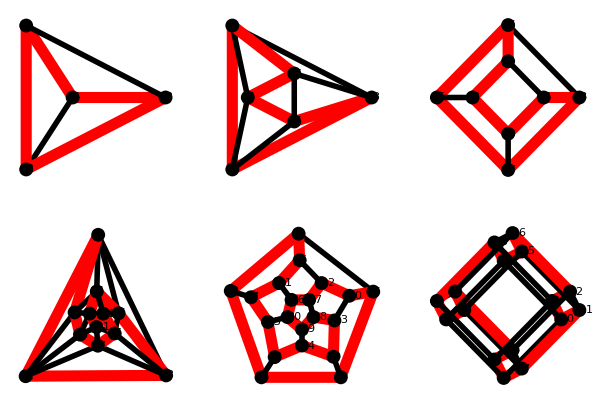

```mathematica
grafo={};
Do[
ciclo=HamiltonianCycle[grafos[[k]]];
ladosciclo=Table[Sort[{ciclo[[i]],ciclo[[i+1]]}],{i,Length[ciclo]-1}];
lados=Edges[grafos[[k]]];
vertices=Vertices[grafos[[k]]];
color={};
grosor={};
Do[
If[Intersection[{Sort[lados[[i]]]},ladosciclo]=={},AppendTo[color,Black];AppendTo[grosor,.01];,AppendTo[color,Red];AppendTo[grosor,.02];];
,{i,Length[lados]}];
AppendTo[grafo,Graph[Table[{lados[[i]],EdgeColor->color[[i]],EdgeStyle->Thickness[grosor[[i]]]},{i,Length[lados]}],Table[{vertices[[i]]},{i,Length[vertices]}]]];
,{k,Length[grafos]}]
ShowGraphArray[{grafo[[1;;3]],grafo[[4;;6]]},VertexLabel->True]
```

```mathematica
Clear[color,grosor]
```

```mathematica
Do[
ciclo=HamiltonianCycle[grafos[[k]]];
ladosciclo=Table[Sort[{ciclo[[i]],ciclo[[i+1]]}],{i,Length[ciclo]-1}];
lados=Edges[grafos[[k]]];
Do[
If[Intersection[{Sort[lados[[i]]]},ladosciclo]=={},
color[Sort[lados[[i]]]]=Yellow;
grosor[Sort[lados[[i]]]]=.02;
,
color[Sort[lados[[i]]]]=Red;
grosor[Sort[lados[[i]]]]=.04;
];
,{i,Length[lados]}];

Print[GraphPlot3D[ToAdjacencyMatrix[grafos[[k]]],VertexRenderingFunction->({Blue,Sphere[#,.1],White,Text[#2,#1]}&),EdgeRenderingFunction->Function[{i,j},{color[Sort[j]],Cylinder[i,grosor[Sort[j]]]}]]];

,{k,Length[grafos]}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»